```mathematica
Clear["`*"];
plotfigs=0;
simType=1;
sims={1,1};
{simi,nsim}={1,20};
garbage=1;gcor=0;
esence=Range[sims⟦2⟧-sims⟦1⟧+1];
pas=1;
avrg[vector_]:=Table[Mean[Mean[vector⟦altfel,asa⟧]],{altfel,Length[vector]},{asa,Length[vector⟦1⟧]}];
avrg[vector_,mask_,window_,npp_]:=Table[GaussianFilter[Mean[Mean[vector⟦altfel,asa⟧ noactparticles⟦asa⟧]]/npp⟦asa⟧,window],{altfel,Length[vector]},{asa,Length[vector⟦1⟧]}];
vit[vector_,scl_,τ_]:=Table[{τ[[as]],(RotateLeft[vector⟦alt,as⟧]-RotateRight[vector⟦alt,as⟧]) scl⟦as⟧}//Transpose,{alt,Length[vector]},{as,Length[vector⟦1⟧]}];
dif[vector1_,vector2_,scl_,τ_]:=Table[{τ[[as]],(RotateLeft[vector1⟦alt,as⟧-vector2⟦alt,as⟧^2]-RotateRight[vector1⟦alt,as⟧-vector2⟦alt,as⟧^2]) scl⟦as⟧}//Transpose,{alt,Length[vector1]},{as,Length[vector1⟦1⟧]}];
colors={Red,Blue,Green,Brown,Orange,Cyan,Black,Gray,Magenta,Pink};graftime[content_,name_]:=ListLinePlot[content,PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"t",name},LabelStyle->{Black,Bold,15,FontFamily->"Times"},ImageSize->Medium,PlotStyle->colors,PlotLegends -> Placed[
  LineLegend[Automatic, LabelStyle -> {FontSize -> 11}],
  {0.9, 0.5}
]];
histo[content_,name_]:=Histogram[content,{1/20 Max[Flatten[content]]},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{name,"P["<>name<>"]"},LabelStyle->{Black,Bold,15,FontFamily->"Times"},ImageSize->Medium,ChartStyle->colors,ChartLegends->Placed[Automatic,{0.9,0.5}]];
histo2[content_,bin_,name_]:=Histogram[content,{bin},PlotRange->Automatic,PlotTheme->"Scientific",FrameLabel->{name,"P["<>name<>"]"},LabelStyle->{Black,Bold,15,FontFamily->"Times"},ImageSize->Medium,ChartStyle->colors,ChartLegends->Placed[Automatic,{0.9,0.5}]];Monitor[For[Simulation=sims⟦1⟧,Simulation≤sims⟦2⟧,Simulation++,Clear[vars,pars,varset,folder,zeros,nvarset,pars,names,safeNames,values,pars,betaD,betaF,FM,X,Y,Z,q1,q2,q3,Vp,μ,data,H,Vtx1GF,Q1GF,Vp1GF,H1GF,Heat1GF,Vtx2GF,Q2GF,Vp2GF,H2GF,Heat2GF,Vtx1FF,Q1FF,Vp1FF,H1FF,Heat1FF,Vtx2FF,Q2FF,Vp2FF,H2FF,Heat2FF,Vtx1DF,Q1DF,Vp1DF,H1DF,Heat1DF,Vtx2DF,Q2DF,Vp2DF,H2DF,Heat2DF,Vtx1FD,Q1FD,Vp1FD,H1FD,Heat1FD,Vtx2FD,Q2FD,Vp2FD,H2FD,Heat2FD,Vtx1DD,Q1DD,Vp1DD,H1DD,Heat1DD,Vtx2DD,Q2DD,Vp2DD,H2DD,Heat2DD,Vn,Dnn,Dnt,Dtt,Xallin,Xallout,Yallin,Yallout,Zallin,Zallout,Vpallin,Vpallout,muallin,muallout,betaFallin,betaFallout,betaDallin,betaDallout,FMallin,F0allin,G0allin,FMallout,Hallout,q1allout,q2allout,Vtxallout,mask2allout,q1allPc,ck1,ck2,ck3,Vcorff,VcorTT,noactparticles,VcorTN,VcorNT,t0,tc,tt,tmax,Nt,Nreal,Nc,Nloop,Np,ntraj,Nci,Nce,Ti,Te,Zeff,Aeff,ndens,vth,rhoi,wi,Ln,Li,Le,magneticmodel,B0,R0,a0,s1,s2,s3,q00,r00,psi0,amp,elong,device,shot,shotslice,NgridR,NgridZ,Omgt0,Omgtprim,turbmodel,xcorr,ycorr,tcorr,Phi,turbprof,Ai,Ae,lambdax,lambday,lambdaz,lbalonz,tauc,k0i,k0e,gammaZF,gammaE,X0,Y0,Z0,Ts,Es,Lns, Lts,pitch,As,Zs,taucc,positiontype,annuluswidth,pitchtype,energytype,Lns,Lts,USElarmor,USEcoll,USEturb,USEmagnturb,USEfreq,USEpolar,USEPC,USEreal,USEcorr,USEballoon,USEtilt,USEtesting,C1,C2,C3];If[simType==1,folder=StringDrop[NotebookDirectory[],-8]<>"data/Sim_";];If[simType==2,folder=StringDrop[NotebookDirectory[],-8]<>"data/DB_";];folder=folder<>IntegerString[Simulation,10,3]<>"/";expfoto=StringTake[folder,StringLength[folder]-15]<>"Arxiv/";nsim2=nsim-simi+1;

varset={wevary,pars,betaD,betaF,FM,X,Y,Z,q1,q2,q3,Vp,μ,data,H,Vtx1GF,Q1GF,Vp1GF,H1GF,Heat1GF,Vtx2GF,Q2GF,Vp2GF,H2GF,Heat2GF,Vtx1FF,Q1FF,Vp1FF,H1FF,Heat1FF,Vtx2FF,Q2FF,Vp2FF,H2FF,Heat2FF,Vtx1DF,Q1DF,Vp1DF,H1DF,Heat1DF,Vtx2DF,Q2DF,Vp2DF,H2DF,Heat2DF,Vtx1FD,Q1FD,Vp1FD,H1FD,Heat1FD,Vtx2FD,Q2FD,Vp2FD,H2FD,Heat2FD,Vtx1DD,Q1DD,Vp1DD,H1DD,Heat1DD,Vtx2DD,Q2DD,Vp2DD,H2DD,Heat2DD,Vn,Dnn,Dnt,Dtt,Xallin,Xallout,Yallin,Yallout,Zallin,Zallout,Vpallin,Vpallout,muallin,muallout,betaFallin,betaFallout,betaDallin,betaDallout,FMallin,F0allin,G0allin,FMallout,Hallout,q1allout,q2allout,Vtxallout,mask2allout,Pc,ck1,ck2,ck3,kx,ky,kz,kperp,w,ph,Vcorff,VcorTT,noactparticles,VcorTN,VcorNT};nvarset=Length[varset];
zeros=Table[0,{i,nvarset},{j,nsim2}];MapThread[Set,{varset,zeros}];varset=ConstantArray[Range[nsim2],Length[varset]];

For[i=simi,i≤nsim,i++,run="Run_"<>StringJoin[Table["0",{i,4-IntegerPart[Log[10.,i]]}]];igood=i-simi+1;dd=Flatten[Import[folder<>run<>ToString[i]<>"/parameters.dat","Table"]];If[simType==1,{dd=Flatten[Import[folder<>run<>ToString[i]<>"/parameters.dat","Table"]];pars⟦igood⟧=dd⟦Position[dd,"t0"]⟦1,1⟧;;Length[dd]⟧;pzpz=Flatten[Position[dd⟦1;;Position[dd,"t0"]⟦1,1⟧⟧,"|"]]⟦4;;5⟧;de=StringRiffle[Rest[Most[dd⟦1;;Position[dd,"t0"]⟦1,1⟧⟧⟦pzpz⟦1⟧;;pzpz⟦2⟧⟧]]];wevary⟦igood⟧=StringRiffle[StringReplace[StringCases[de,"sweeps="~~rest___:>StringCases[rest,x:(Except["("|","|" "]..)~~"(":>x]]⟦1⟧,"_"->""]," & "];};];If[simType==2,{dd=Flatten[Import[folder<>run<>ToString[i]<>"/parameters.dat","Table"]];pars⟦igood⟧=dd⟦Position[dd,"t0"]⟦1,1⟧;;Length[dd]⟧;pzpz=Flatten[Position[dd⟦1;;Position[dd,"t0"]⟦1,1⟧⟧,"|"]]⟦3;;4⟧;de=StringRiffle[Rest[Most[dd⟦1;;Position[dd,"t0"]⟦1,1⟧⟧⟦pzpz⟦1⟧;;pzpz⟦2⟧⟧]]];wevary⟦igood⟧=StringReplace[First[StringCases[de,"selection=Vary_ "~~x:(Except["\""]..)~~"_only":>x]],"_"->""];};];len=IntegerPart[1/2 Length[pars⟦igood⟧]];{names,values}={pars⟦igood,1;;len⟧,pars⟦igood,len+1;;2 len⟧};safeNames=StringReplace[names,"_"->""];vars=Symbol/@safeNames;MapThread[Set,{vars,values}];{Nreal,Nc,Np,Nt,Nloop,ntraj}=Rationalize[{Nreal,Nc,Np,Nt,Nloop,ntraj}];

noactparticles⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/mask.bin","Real64"],{Nreal,Nloop}];If[garbage==1,{X⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/Xtraj.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];Y⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/Ytraj.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];Z⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/Ztraj.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];Vp⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/Vptraj.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];μ⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/mutraj.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];betaF⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/betaFtraj.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];betaD⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/betaDtraj.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];FM⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/FMtraj.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];H⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/Htraj.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];q1⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/q1traj.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];q2⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/q2traj.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];q3⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/q3traj.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];Pc⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/Pctraj.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];ck1⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/ck1traj.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];ck2⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/ck2traj.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];ck3⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/ck3traj.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];Xallin⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/Xinit.bin","Real64"];Yallin⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/Yinit.bin","Real64"];Zallin⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/Zinit.bin","Real64"];Vpallin⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/Vpinit.bin","Real64"];muallin⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/muinit.bin","Real64"];betaFallin⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/betaFinit.bin","Real64"];Xallout⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/Xout.bin","Real64"];Yallout⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/Yout.bin","Real64"];Zallout⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/Zout.bin","Real64"];Vpallout⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/Vpout.bin","Real64"];muallout⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/muout.bin","Real64"];betaFallout⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/betaFout.bin","Real64"];FMallin⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/FMinit.bin","Real64"];F0allin⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/F0init.bin","Real64"];G0allin⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/G0init.bin","Real64"];FMallout⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/FMout.bin","Real64"];Hallout⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/Hout.bin","Real64"];q1allout⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/q1out.bin","Real64"];q2allout⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/q2out.bin","Real64"];

Vtxallout⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/Vtxout.bin","Real64"];
mask2allout⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/mask2out.bin","Real64"];

betaDallin⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/betaDinit.bin","Real64"];betaDallout⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/betaDout.bin","Real64"];}];


If[gcor==1,Vcorff⟦igood⟧=Mean[Mean[ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/Vcorff.bin","Real64"],{Nreal,Nloop,Nt+1,Nt+1}]]];VcorTT⟦igood⟧=Mean[Mean[ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/VcorTT.bin","Real64"],{Nreal,Nloop,Nt+1,Nt+1}]]];VcorTN⟦igood⟧=Mean[Mean[ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/VcorTN.bin","Real64"],{Nreal,Nloop,Nt+1,Nt+1}]]];VcorNT⟦igood⟧=Mean[Mean[ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/VcorNT.bin","Real64"],{Nreal,Nloop,Nt+1,Nt+1}]]];];VcorNN=Vcorff-VcorTT-VcorNT-VcorTN;

dar=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/Obs_GF.bin","Real64"],{Nreal,Nloop,Nt+1,10}];{Vtx1GF⟦igood⟧,Q1GF⟦igood⟧,Vp1GF⟦igood⟧,H1GF⟦igood⟧,Heat1GF⟦igood⟧,Vtx2GF⟦igood⟧,Q2GF⟦igood⟧,Vp2GF⟦igood⟧,H2GF⟦igood⟧,Heat2GF⟦igood⟧}=Table[dar⟦All,All,All,is⟧,{is,10}];dar=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/Obs_FF.bin","Real64"],{Nreal,Nloop,Nt+1,10}];{Vtx1FF⟦igood⟧,Q1FF⟦igood⟧,Vp1FF⟦igood⟧,H1FF⟦igood⟧,Heat1FF⟦igood⟧,Vtx2FF⟦igood⟧,Q2FF⟦igood⟧,Vp2FF⟦igood⟧,H2FF⟦igood⟧,Heat2FF⟦igood⟧}=Table[dar⟦All,All,All,is⟧,{is,10}];dar=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/Obs_DF.bin","Real64"],{Nreal,Nloop,Nt+1,10}];{Vtx1DF⟦igood⟧,Q1DF⟦igood⟧,Vp1DF⟦igood⟧,H1DF⟦igood⟧,Heat1DF⟦igood⟧,Vtx2DF⟦igood⟧,Q2DF⟦igood⟧,Vp2DF⟦igood⟧,H2DF⟦igood⟧,Heat2DF⟦igood⟧}=Table[dar⟦All,All,All,is⟧,{is,10}];dar=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/Obs_FD.bin","Real64"],{Nreal,Nloop,Nt+1,10}];{Vtx1FD⟦igood⟧,Q1FD⟦igood⟧,Vp1FD⟦igood⟧,H1FD⟦igood⟧,Heat1FD⟦igood⟧,Vtx2FD⟦igood⟧,Q2FD⟦igood⟧,Vp2FD⟦igood⟧,H2FD⟦igood⟧,Heat2FD⟦igood⟧}=Table[dar⟦All,All,All,is⟧,{is,10}];dar=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/Obs_DD.bin","Real64"],{Nreal,Nloop,Nt+1,10}];{Vtx1DD⟦igood⟧,Q1DD⟦igood⟧,Vp1DD⟦igood⟧,H1DD⟦igood⟧,Heat1DD⟦igood⟧,Vtx2DD⟦igood⟧,Q2DD⟦igood⟧,Vp2DD⟦igood⟧,H2DD⟦igood⟧,Heat2DD⟦igood⟧}=Table[dar⟦All,All,All,is⟧,{is,10}];

dar=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/Obs_SS.bin","Real64"],{Nreal,Nloop,Nt+1,4}];{Vn⟦igood⟧,Dnn⟦igood⟧,Dnt⟦igood⟧,Dtt[[igood]]}=Table[dar⟦All,All,All,is⟧,{is,4}];


Clear@@safeNames;

];dt=tmax/Nt;ρ=√((X-1.)^2+Y^2);z=Y;x=X Cos[Z];y=X Sin[Z];θ=ArcTan[X-1,Y];
Thread[Evaluate[ToExpression[vars]]=Transpose[pars⟦All,1+len;;2 len⟧]];
t=Table[dt⟦as⟧ (Range[Nt⟦as⟧+1]-1),{as,Length[Q1FF]}];
(*loop averaged and smoothed quantities*)

{Vtx1GF,Q1GF,Vp1GF,H1GF,Heat1GF,Vtx2GF,Q2GF,Vp2GF,H2GF,Heat2GF,Vtx1FF,Q1FF,Vp1FF,H1FF,Heat1FF,Vtx2FF,Q2FF,Vp2FF,H2FF,Heat2FF,Vtx1DF,Q1DF,Vp1DF,H1DF,Heat1DF,Vtx2DF,Q2DF,Vp2DF,H2DF,Heat2DF,Vtx1FD,Q1FD,Vp1FD,H1FD,Heat1FD,Vtx2FD,Q2FD,Vp2FD,H2FD,Heat2FD,Vtx1DD,Q1DD,Vp1DD,H1DD,Heat1DD,Vtx2DD,Q2DD,Vp2DD,H2DD,Heat2DD,Vn,Dnn, Dnt, Dtt}=avrg[{Vtx1GF,Q1GF,Vp1GF,H1GF,Heat1GF,Vtx2GF,Q2GF,Vp2GF,H2GF,Heat2GF,Vtx1FF,Q1FF,Vp1FF,H1FF,Heat1FF,Vtx2FF,Q2FF,Vp2FF,H2FF,Heat2FF,Vtx1DF,Q1DF,Vp1DF,H1DF,Heat1DF,Vtx2DF,Q2DF,Vp2DF,H2DF,Heat2DF,Vtx1FD,Q1FD,Vp1FD,H1FD,Heat1FD,Vtx2FD,Q2FD,Vp2FD,H2FD,Heat2FD,Vtx1DD,Q1DD,Vp1DD,H1DD,Heat1DD,Vtx2DD,Q2DD,Vp2DD,H2DD,Heat2DD,Vn,Dnn, Dnt, Dtt},noactparticles,pas,Np];
scale={rhoi/(R0/vth),1+0rhoi,1+0vth,1+0Ti,Ti*rhoi/(R0/vth)(*Ti*),(rhoi/(R0/vth))^2,1+0(rhoi/1)^2,1+0 vth^2,1+0Ti,Ti*rhoi/(R0/vth)};
{Vn,Dnn, Dnt, Dtt}={rhoi/(R0/vth)Vn,R0/vth(rhoi/(R0/vth))^2 Dnn,R0/vth(rhoi/(R0/vth))^2 Dnt,R0/vth(rhoi/(R0/vth))^2 Dtt};

{Vtx1GF,Q1GF,Vp1GF,H1GF,Heat1GF,Vtx2GF,Q2GF,Vp2GF,H2GF,Heat2GF,Vtx1FF,Q1FF,Vp1FF,H1FF,Heat1FF,Vtx2FF,Q2FF,Vp2FF,H2FF,Heat2FF,Vtx1DF,Q1DF,Vp1DF,H1DF,Heat1DF,Vtx2DF,Q2DF,Vp2DF,H2DF,Heat2DF,Vtx1FD,Q1FD,Vp1FD,H1FD,Heat1FD,Vtx2FD,Q2FD,Vp2FD,H2FD,Heat2FD,Vtx1DD,Q1DD,Vp1DD,H1DD,Heat1DD,Vtx2DD,Q2DD,Vp2DD,H2DD,Heat2DD}=ArrayReshape[Table[scale,{io,5}],{50,nsim2}]{Vtx1GF,Q1GF,Vp1GF,H1GF,Heat1GF,Vtx2GF,Q2GF,Vp2GF,H2GF,Heat2GF,Vtx1FF,Q1FF,Vp1FF,H1FF,Heat1FF,Vtx2FF,Q2FF,Vp2FF,H2FF,Heat2FF,Vtx1DF,Q1DF,Vp1DF,H1DF,Heat1DF,Vtx2DF,Q2DF,Vp2DF,H2DF,Heat2DF,Vtx1FD,Q1FD,Vp1FD,H1FD,Heat1FD,Vtx2FD,Q2FD,Vp2FD,H2FD,Heat2FD,Vtx1DD,Q1DD,Vp1DD,H1DD,Heat1DD,Vtx2DD,Q2DD,Vp2DD,H2DD,Heat2DD};

scale=rhoi/((R0 (2 t⟦All,2⟧))/vth);
{𝒱GF,𝒱FF,𝒱FD,𝒱DF,𝒱DD}=vit[{Q1GF,Q1FF,Q1FD,Q1DF,Q1DD},scale,t];
scale=rhoi^2/((R0 (4t⟦All,2⟧))/vth);
{𝒟GF,𝒟FF,𝒟FD,𝒟DF,𝒟DD}=dif[{Q2GF,Q2FF,Q2FD,Q2DF,Q2DD},{Q1GF,Q1FF,Q1FD,Q1DF,Q1DD},scale,t];


𝒟GF⟦All,1,2⟧=𝒟GF⟦All,2,2⟧ 0;
𝒟FF⟦All,1,2⟧=𝒟FF⟦All,2,2⟧ 0;
𝒟FD⟦All,1,2⟧=𝒟FD⟦All,2,2⟧ 0;
𝒟DF⟦All,1,2⟧=𝒟DF⟦All,2,2⟧ 0;
𝒟DD⟦All,1,2⟧=𝒟DD⟦All,2,2⟧ 0;
𝒱GF⟦All,1,2⟧=𝒱GF⟦All,2,2⟧;
𝒱FF⟦All,1,2⟧=𝒱FF⟦All,2,2⟧;
𝒱FD⟦All,1,2⟧=𝒱FD⟦All,2,2⟧;
𝒱DF⟦All,1,2⟧=𝒱DF⟦All,2,2⟧;
𝒱DD⟦All,1,2⟧=𝒱DD⟦All,2,2⟧;

For[i=1,i≤nsim2,i++,𝒟GF⟦i,Nt⟦i⟧+1,2⟧=𝒟GF⟦i,Nt⟦i⟧,2⟧;𝒟FF⟦i,Nt⟦i⟧+1,2⟧=𝒟FF⟦i,Nt⟦i⟧,2⟧;𝒟FD⟦i,Nt⟦i⟧+1,2⟧=𝒟FD⟦i,Nt⟦i⟧,2⟧;𝒟DF⟦i,Nt⟦i⟧+1,2⟧=𝒟DF⟦i,Nt⟦i⟧,2⟧;𝒟DD⟦i,Nt⟦i⟧+1,2⟧=𝒟DD⟦i,Nt⟦i⟧,2⟧;𝒱GF⟦i,Nt⟦i⟧+1,2⟧=𝒱GF⟦i,Nt⟦i⟧,2⟧;𝒱FF⟦i,Nt⟦i⟧+1,2⟧=𝒱FF⟦i,Nt⟦i⟧,2⟧;𝒱FD⟦i,Nt⟦i⟧+1,2⟧=𝒱FD⟦i,Nt⟦i⟧,2⟧;𝒱DF⟦i,Nt⟦i⟧+1,2⟧=𝒱DF⟦i,Nt⟦i⟧,2⟧;𝒱DD⟦i,Nt⟦i⟧+1,2⟧=𝒱DD⟦i,Nt⟦i⟧,2⟧;];
frac=0.5;frac2=0.95;VQas=Table[Mean[𝒱GF⟦i,IntegerPart[frac Nt⟦i⟧];;IntegerPart[Nt⟦i⟧-1],2⟧],{i,nsim2}];DQas=Table[Mean[𝒟GF⟦i,IntegerPart[frac Nt⟦i⟧];;IntegerPart[Nt⟦i⟧-1],2⟧],{i,nsim2}];

{ϵ0,logL,e,mi}={8.85/10^12,17.,1.6/10^19,1.6/10^27};
nub0=(4.0 logL ndens ((Zeff Zs e^2)/(ϵ0 mi As))^2 (√(Aeff/2.0))^3)/((8.0 π) vth^3);nub=((4.0 logL ndens ((Zeff Zs e^2)/(ϵ0 mi As))^2 (√(Aeff/2.0))^3) ((r00 R0) q00 √2))/(((8.0 π) vth^3) (vth √r00));Γgyro=(rhoi/(a0 R0))^2 vth As;
esence⟦Simulation-sims⟦1⟧+1⟧={wevary⟦1⟧,ToExpression[wevary⟦1⟧],VQas,DQas};If[plotfigs==1,{pozvar=len+{19,15,32,34,26,27,42,44,46,47,48,50,53,63,66}⟦Simulation⟧;pozvar=len+{49,66,21,47,63,67,58,51,52,53,54,55}⟦Simulation⟧;cine=names⟦pozvar-len⟧;cat=pars⟦All,pozvar⟧;fig1={ListPlot[Transpose[{cat,VQas}],PlotTheme->"Scientific",FrameLabel->{cine,"V[\!\(\*SuperscriptBox[\(m\), \(2\)]\)/s]"},LabelStyle->{Black,Bold,18},ImageSize->500,Joined->True,PlotMarkers->Automatic,PlotRange->All],ListPlot[Transpose[{cat,DQas}],PlotTheme->"Scientific",FrameLabel->{cine,"D[\!\(\*SuperscriptBox[\(m\), \(2\)]\)/s]"},LabelStyle->{Black,Bold,18},ImageSize->500,Joined->True,PlotMarkers->Automatic,PlotRange->All]};fig2={ListPlot[𝒱FF,PlotTheme->"Scientific",FrameLabel->{"t[R0/\!\(\*SubscriptBox[\(v\), \(th\)]\)]","V[\!\(\*SuperscriptBox[\(m\), \(2\)]\)/s]"},LabelStyle->{Black,Bold,18},ImageSize->500,Joined->True,PlotRange->Automatic],ListPlot[𝒟FF,PlotTheme->"Scientific",FrameLabel->{"t[R0/\!\(\*SubscriptBox[\(v\), \(th\)]\)]","D[\!\(\*SuperscriptBox[\(m\), \(2\)]\)/s]"},LabelStyle->{Black,Bold,18},ImageSize->500,Joined->True,PlotRange->All]};nmax=Min[10^4,Np⟦1⟧];fig3=Table[ListPlot[{Transpose[{Xallout⟦as,1;;nmax⟧,Yallout⟦as,1;;nmax⟧}],Transpose[{Xallin⟦as,1;;nmax⟧,Yallin⟦as,1;;nmax⟧}]},PlotRange->All,PlotStyle->{Red,Blue}],{as,nsim2}];Export[folder<>"fig_1_a.png",fig1⟦1⟧];Export[folder<>"fig_1_b.png",fig1⟦2⟧];Export[folder<>"fig_2_a.png",fig2⟦1⟧];Export[folder<>"fig_2_b.png",fig2⟦2⟧];If[garbage==1,For[as=1,as≤nsim2,as++,Export[folder<>"fig_3_"<>ToString[as]<>".png",fig3⟦as⟧]];];}];],{Row[{ProgressIndicator[i,{1,nsim2}],ToString[i]<>"/"<>ToString[nsim2]}],Row[{ProgressIndicator[Simulation,{sims⟦1⟧,sims⟦2⟧}],ToString[Simulation]<>"/"<>ToString[sims⟦2⟧-sims⟦1⟧]}]}];
```

```mathematica
(*PHASE SPACE REPRESENTATION*)
```

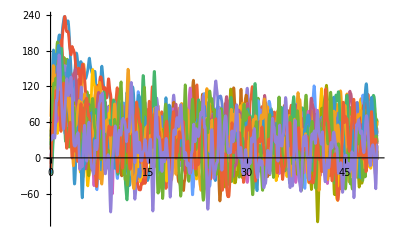

```mathematica
ListLinePlot[𝒱FF,PlotRange->All]
```

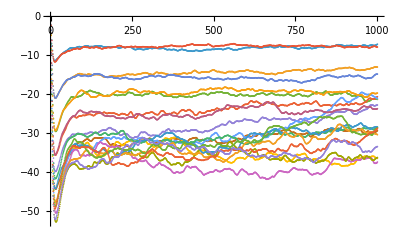

```mathematica
ListPlot[Vn,PlotRange->All]
```

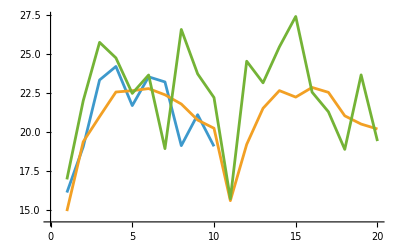

```mathematica
{𝒹DD,DQas,Dnn[[All,700;;1000]]//Transpose//Mean}//ListLinePlot
```

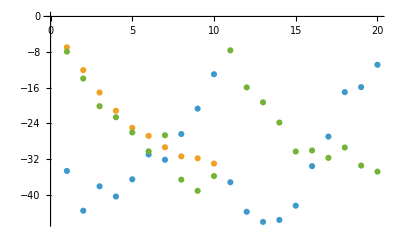

```mathematica
{-VQas,𝓋DD,Vn[[All,500;;1000]]//Transpose//Mean}//ListPlot
```

```mathematica
as=2;ntr=10^3;
h[z9_,σ9_]=Exp[-z9^2/(2 σ9)]/(√(π/2) √σ9 2);
weights=((FMallout⟦as⟧ (Exp[betaDallout⟦as⟧]-0 1))/G0allin⟦as⟧)⟦1;;ntr⟧;
σ=1/200 ({Max[Xallout⟦as⟧]-Min[Xallout⟦as⟧],Max[Yallout⟦as⟧]-Min[Yallout⟦as⟧],Max[Zallout⟦as⟧]-Min[Zallout⟦as⟧],Max[Vpallout⟦as⟧]-Min[Vpallout⟦as⟧],Max[muallout⟦as⟧]-Min[muallout⟦as⟧]}^2)⟦1;;2⟧;
particles={Xallout,Yallout,Zallout,Vpallout,muallout}⟦1;;2,as,1;;ntr⟧;
ngrid=10000;
grid={RandomReal[{0.7,1.3},ngrid],RandomReal[{-.3,.3},ngrid],RandomReal[{-π,π},ngrid],RandomReal[{-3,3},ngrid],RandomReal[{0,5},ngrid]}⟦1;;2⟧;
densityout=ParallelTable[h[grid⟦1,j⟧-particles⟦1⟧,σ⟦1⟧] h[grid⟦2,j⟧-particles⟦2⟧,σ⟦2⟧],{j,Length[grid⟦1⟧]}].weights;
weights=((FMallin⟦as⟧ (Exp[betaDallin⟦as⟧]-0 1))/G0allin⟦as⟧)⟦1;;ntr⟧;
particles={Xallin,Yallin,Zallin,Vpallin,muallin}⟦1;;2,as,1;;ntr⟧;
densityin=ParallelTable[h[grid⟦1,j⟧-particles⟦1⟧,σ⟦1⟧] h[grid⟦2,j⟧-particles⟦2⟧,σ⟦2⟧],{j,Length[grid⟦1⟧]}].weights;
```

```mathematica
ListPointPlot3D[Transpose[{grid⟦1⟧,grid⟦2⟧,densityout}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Transpose[{grid⟦1⟧,grid⟦2⟧,densityout-densityin}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListDensityPlot[Transpose[{grid⟦1⟧,grid⟦2⟧,densityout-densityin}],PlotRange->All,ColorFunction->Hue]
```

-Graphics-

```mathematica
as=1;ntr=10^3;
h[z9_,σ9_]=Exp[-z9^2/(2 σ9)]/(√(π/2) √σ9 2);
weights=((FMallout⟦as⟧ (Exp[betaDallout⟦as⟧]-0 1))/G0allin⟦as⟧)[[1;;ntr]];
σ={1/100 (Max[Vpallout⟦as⟧]-Min[Vpallout⟦as⟧]),1/100 (Max[muallout⟦as⟧]-Min[muallout⟦as⟧])}^2;
particles={Xallout,Yallout,Zallout,Vpallout,muallout}⟦4;;5,as,1;;ntr⟧;
ngrid=10000;
grid={RandomReal[{-3,3},ngrid],RandomReal[{0,5},ngrid]};
densityout=ParallelTable[h[grid[[1,j]]-particles[[1]],σ[[1]]] h[grid[[2,j]]-particles[[2]],σ[[2]]],{j,Length[grid[[1]]]}].weights;
weights=((FMallin⟦as⟧ (Exp[betaDallin⟦as⟧]-0 1))/G0allin⟦as⟧)[[1;;ntr]];
particles={Xallin,Yallin,Zallin,Vpallin,muallin}⟦4;;5,as,1;;ntr⟧;
densityin=ParallelTable[h[grid[[1,j]]-particles[[1]],σ[[1]]] h[grid[[2,j]]-particles[[2]],σ[[2]]],{j,Length[grid[[1]]]}].weights;
```

```mathematica
ListPointPlot3D[Transpose[{grid⟦1⟧,grid⟦2⟧,densityout}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Transpose[{grid⟦1⟧,grid⟦2⟧,densityout-densityin}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListDensityPlot[Transpose[{grid⟦1⟧,grid⟦2⟧,densityout-densityin}],PlotRange->All,ColorFunction->Hue]
```

-Graphics-

```mathematica
histo2[{Flatten[(FMallout Exp[betaFallout])/F0allin-1]},10^-7,"F0"]
```

$Aborted

```mathematica
frac=0.7;Γ=Mean/@Transpose/@{Vtx1GF,Vtx1FF,Vtx1FD,Vtx1DF,Vtx1DD}⟦All,All,Floor[Nt⟦1⟧ frac];;Nt⟦1⟧⟧;𝓋={𝓋GF,𝓋FF,𝓋FD,𝓋DF,𝓋DD}=Γ⟦All,1;;1/2 Length[Γ⟦1⟧]⟧;
𝒹={𝒹GF,𝒹FF,𝒹FD,𝒹DF,𝒹DD}=-Transpose[(Γ⟦All,1/2 Length[Γ⟦1⟧]+1;;Length[Γ⟦1⟧]⟧-Γ⟦All,1;;1/2 Length[Γ⟦1⟧]⟧)]*R0⟦1/2 Length[Γ⟦1⟧]+1;;Length[Γ⟦1⟧]⟧/Lns⟦1/2 Length[Γ⟦1⟧]+1;;Length[Γ⟦1⟧]⟧//Transpose;
𝒟={𝒟GF,𝒟FF,𝒟FD,𝒟DF,𝒟DD};
𝒱={𝒱GF,𝒱FF,𝒱FD,𝒱DF,𝒱DD};
```

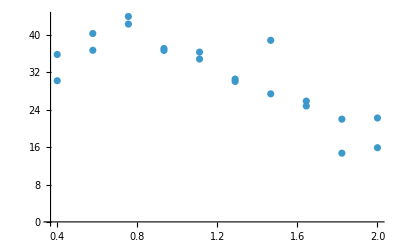

```mathematica
{Zs,VQas}//Transpose//ListPlot
```

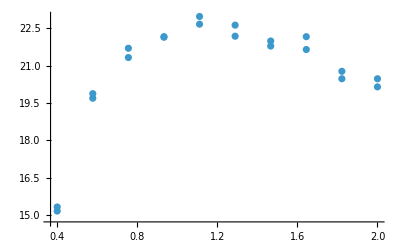

```mathematica
{Zs,DQas}//Transpose//ListPlot
```

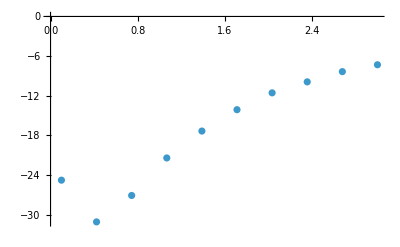
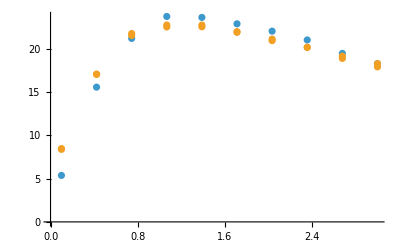

```mathematica
{{Ts[[1;;10]],𝓋DD}//Transpose//ListPlot,{{Ts[[1;;10]],𝒹DD}//Transpose,{Ts,DQas}//Transpose}//ListPlot}
```

```mathematica
Export[StringTake[folder,StringLength[folder]-8]<>"compare_"<>ToString[Simulation-1]<>".dat",{Zs[[1;;10]],𝓋DD,𝒹DD}//Transpose]
```

/home/dragos.palade/Work/FAST/25_05_2026/data/compare_1.dat

```mathematica
Export[StringTake[folder,StringLength[folder]-8]<>"compare_"<>ToString[Simulation-1]<>".dat",{As[[1;;10]],𝓋DD,𝒹DD}//Transpose]
```

/home/dragos.palade/Work/FAST/25_05_2026/data/compare_2.dat

```mathematica
Export[StringTake[folder,StringLength[folder]-8]<>"compare_"<>ToString[Simulation-1]<>".dat",{Ts[[1;;10]],𝓋DD,𝒹DD}//Transpose]
```

/home/dragos.palade/Work/FAST/25_05_2026/data/compare_3.dat

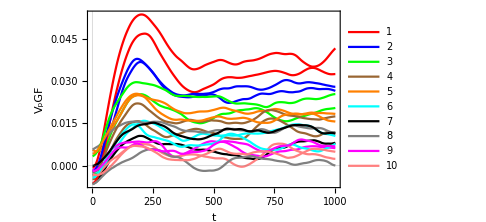
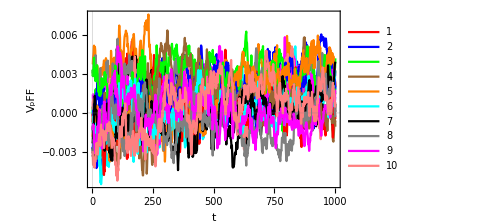
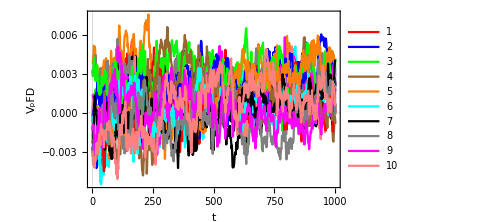
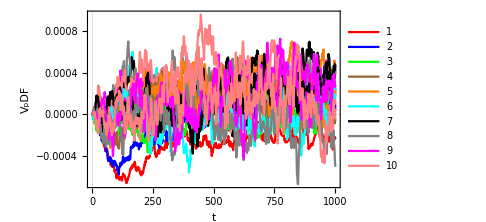
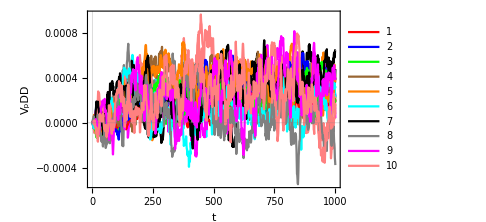

```mathematica
{graftime[Vp1GF,"V_pGF"],graftime[Vp1FF,"V_pFF"],graftime[Vp1FD,"V_pFD"],graftime[Vp1DF,"V_pDF"],graftime[Vp1DD,"V_pDD"]}
```

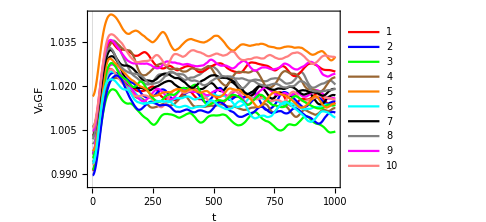
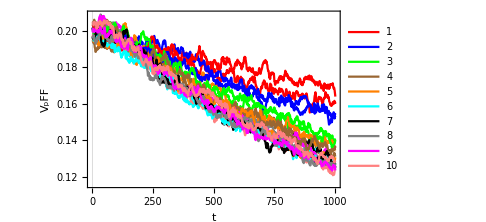
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{graftime[Vp2GF,"V_pGF"],graftime[Vp2FF,"V_pFF"],graftime[Vp1FD,"V_pFD"],graftime[Vp1DF,"V_pDF"],graftime[Vp1DD,"V_pDD"]}
```

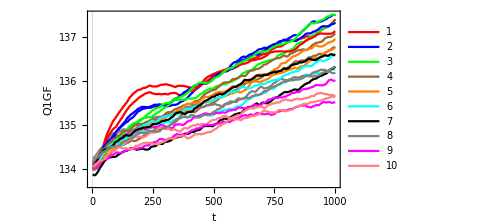
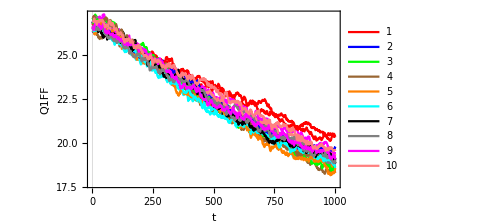
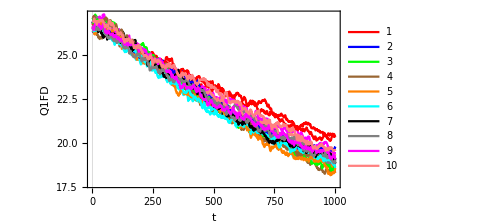
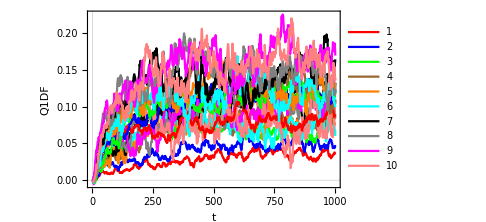
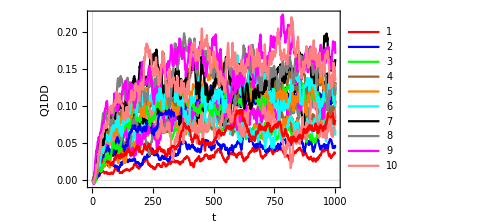

```mathematica
{graftime[Q1GF,"Q1GF"],graftime[Q1FF,"Q1FF"],graftime[Q1FD,"Q1FD"],graftime[Q1DF,"Q1DF"],graftime[Q1DD,"Q1DD"]}
```

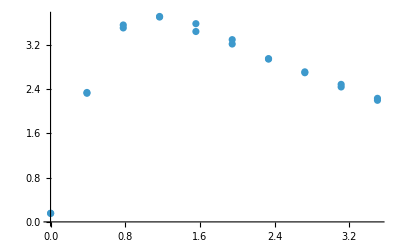

```mathematica
{Ts,DQas}//Transpose//ListPlot
```

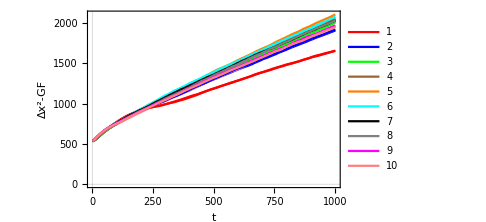
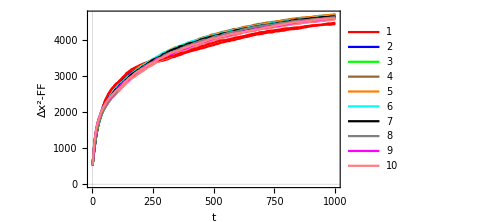
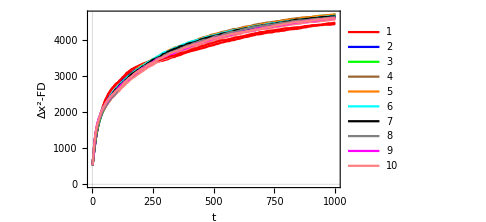
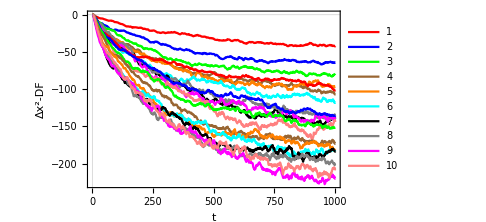
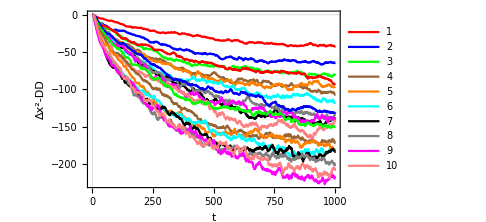

```mathematica
label="Δx^2-";{graftime[Q2GF-Q1GF^2,label<>"GF"],graftime[Q2FF-Q1FF^2,label<>"FF"],graftime[Q2FD-Q1FD^2,label<>"FD"],graftime[Q2DF-Q1DF^2,label<>"DF"],graftime[Q2DD-Q1DD^2,label<>"DD"]}
```

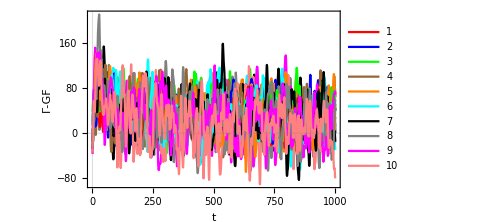
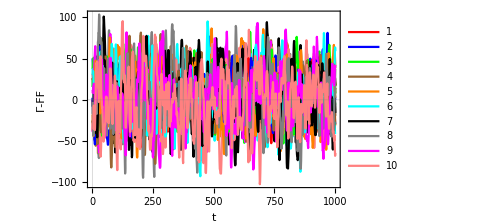
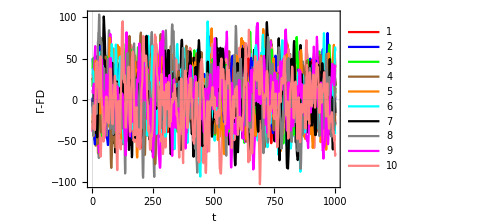
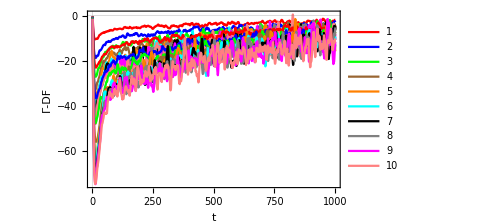
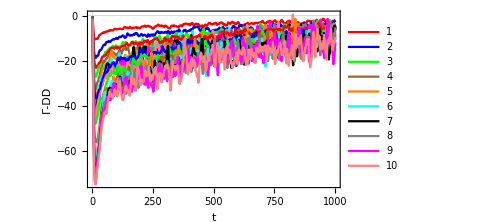

```mathematica
label="Γ-";{graftime[Vtx1GF,label<>"GF"],graftime[Vtx1FF,label<>"FF"],graftime[Vtx1FD,label<>"FD"],graftime[Vtx1DF,label<>"DF"],graftime[Vtx1DD,label<>"DD"]}
```

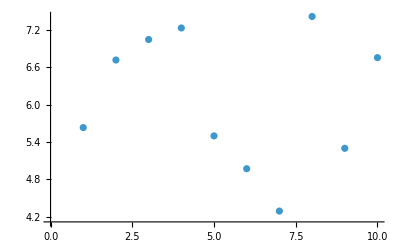

```mathematica
𝒹DD//ListPlot
```

```mathematica
frac=0.7;Γ=Mean/@Transpose/@{Vtx1GF,Vtx1FF,Vtx1FD,Vtx1DF,Vtx1DD}⟦All,All,Floor[Nt⟦1⟧ frac];;Nt⟦1⟧⟧;𝓋={𝓋GF,𝓋FF,𝓋FD,𝓋DF,𝓋DD}=Γ⟦All,1;;1/2 Length[Γ⟦1⟧]⟧;
𝒹={𝒹GF,𝒹FF,𝒹FD,𝒹DF,𝒹DD}=-(R0⟦1/2 Length[Γ⟦1⟧]+1;;Length[Γ⟦1⟧]⟧ (Γ⟦All,1/2 Length[Γ⟦1⟧]+1;;Length[Γ⟦1⟧]⟧-Γ⟦All,1;;1/2 Length[Γ⟦1⟧]⟧))/Lns⟦1/2 Length[Γ⟦1⟧]+1;;Length[Γ⟦1⟧]⟧;
𝒟={𝒟GF,𝒟FF,𝒟FD,𝒟DF,𝒟DD};
𝒱={𝒱GF,𝒱FF,𝒱FD,𝒱DF,𝒱DD};
```

## Ce e cu semnele alea la Q1, Q2...ceva nu e in regula;

## Problema 1 : Care sunt diferentele dintre metode, la ce nivel si de ce? d_t Q, vs Vx, vs FD,DD.etc - it checks out that A_FF-A_FD=A_DF-A_DD=A_fm this is good; - it checks out that A_FD-A_DD=A_FF-A_DF=?? this is good; Γ_FF~ Γ_FD ; also Γ_DF~ Γ_DD but there are serious differences between Γ_FF and Γ_DF;

```mathematica
Obs_FF - Obs_FD = 0
```

```mathematica
quan(10:20)-quan(10+j)
```

```mathematica
Table[Mean[Abs[Q1FF⟦i⟧-Q1FD⟦i⟧]],{i,Length[Q1FF]}]/Table[Mean[Abs[Q1DF⟦i⟧-Q1DD⟦i⟧]],{i,Length[Q1FF]}]
Table[Mean[Abs[Q1FD⟦i⟧-Q1DD⟦i⟧]],{i,Length[Q1FF]}]/Table[Mean[Abs[Q1FF⟦i⟧-Q1DF⟦i⟧]],{i,Length[Q1FF]}]
```

{18.8577,46.4385,45.5223,46.4665,62.7484,76.7441,57.4787,62.7487,94.0709,60.5857,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Table[Mean[Abs[Q2FF⟦i⟧-Q2FD⟦i⟧]],{i,Length[Q1FF]}]/Table[Mean[Abs[Q2DF⟦i⟧-Q2DD⟦i⟧]],{i,Length[Q1FF]}]
Table[Mean[Abs[Q2FD⟦i⟧-Q2DD⟦i⟧]],{i,Length[Q1FF]}]/Table[Mean[Abs[Q2FF⟦i⟧-Q2DF⟦i⟧]],{i,Length[Q1FF]}]
```

{16.9374,21.0999,20.0636,24.3308,44.0205,44.0493,58.99,83.4829,61.0035,41.4622,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Table[Mean[Abs[Vtx1FF⟦i⟧-Vtx1FD⟦i⟧]],{i,Length[Q1FF]}]/Table[Mean[Abs[Vtx1DF⟦i⟧-Vtx1DD⟦i⟧]],{i,Length[Q1FF]}]
Table[Mean[Abs[Vtx1FD⟦i⟧-Vtx1DD⟦i⟧]],{i,Length[Q1FF]}]/Table[Mean[Abs[Vtx1FF⟦i⟧-Vtx1DF⟦i⟧]],{i,Length[Q1FF]}]
```

{1.12731,1.60685,2.47966,2.69145,4.00138,4.54672,4.98052,4.55041,4.55918,6.09891,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

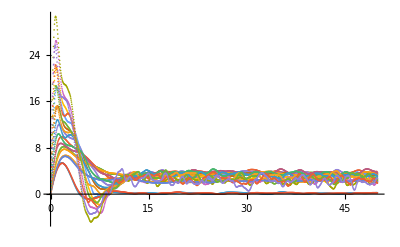

```mathematica
ListPlot[𝒟FD,PlotRange->All]
```

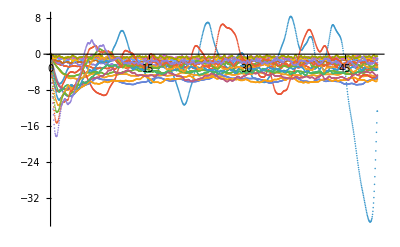

```mathematica
ListPlot[𝒟DF,PlotRange->All]
```

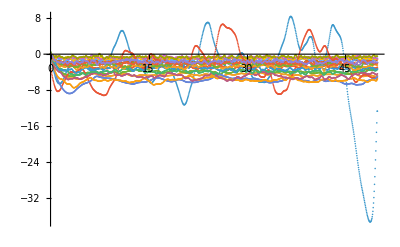

```mathematica
ListPlot[𝒟DD,PlotRange->All]
```

## There are 2 loose questions: why Γ_FF leads to negative diffusion (or chaotic); why there is no consistentcy

## Problema 2: Sunt trendurile coerente intre metode?

## Problema 3: Cum afecteaza width rezultatele?

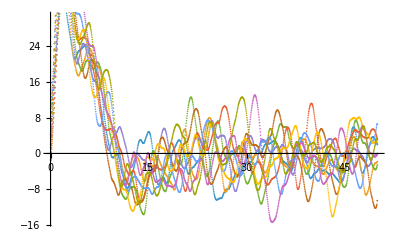

```mathematica
𝒱FD//ListPlot
```

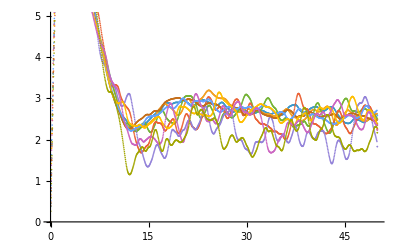

```mathematica
𝒟GF//ListPlot
```

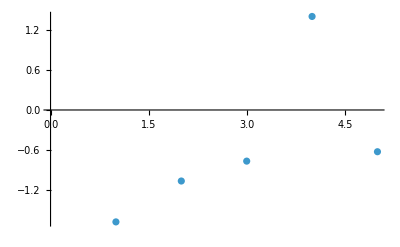

```mathematica
𝓋GF//ListPlot
```

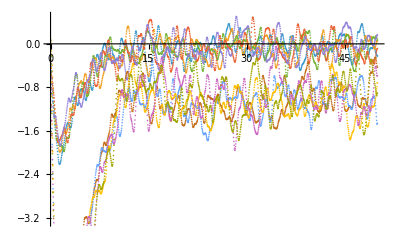

```mathematica
𝒟DF//ListPlot
```

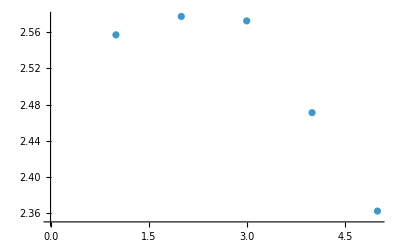

```mathematica
𝒹DF//ListPlot
```

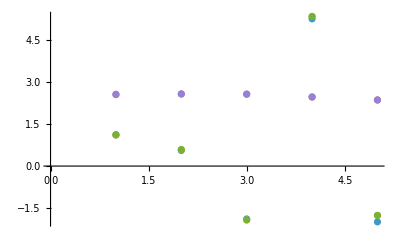

```mathematica
𝒹//ListPlot
```

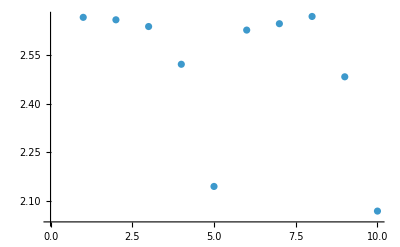

```mathematica
DQas//ListPlot
```

## Problema 4: Ar trebui facuta o masca doar pe un anulus mai ingust? ce inseamna asta?

## Problema 2: Sunt trendurile coerente intre metode?

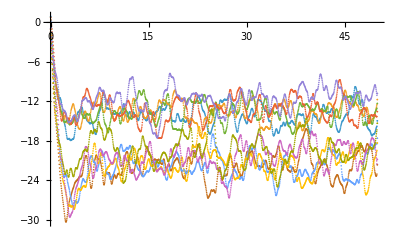

```mathematica
ListPlot[𝒱DD,PlotRange->All]
```

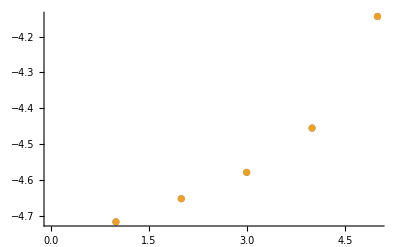
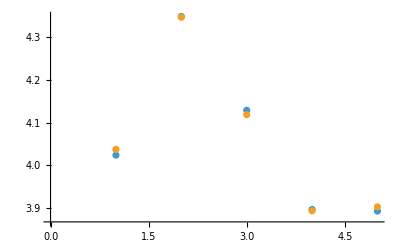

```mathematica
{𝓋[[4;;5]]//ListPlot,𝒹[[4;;5]]//ListPlot}
```

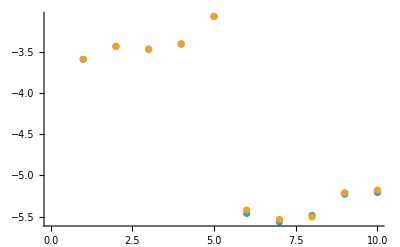
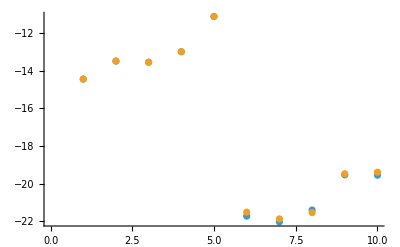

```mathematica
{Map[Mean,𝒟[[All,All,Floor[Nt⟦1⟧ frac];;Nt⟦1⟧,2]],{2}][[4;;5]]//ListPlot,Map[Mean,𝒱[[All,All,Floor[Nt⟦1⟧ frac];;Nt⟦1⟧,2]],{2}][[4;;5]]//ListPlot}
```

{-Graphics-,-Graphics-}

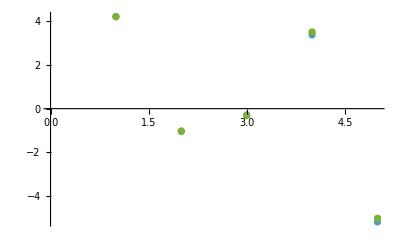

```mathematica
{Map[Mean,𝒟[[All,All,Floor[Nt⟦1⟧ frac];;Nt⟦1⟧,2]],{2}][[4;;5]]//ListPlot,𝒹[[4;;5]]//ListPlot}
```

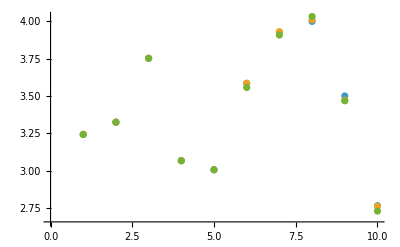
{-Graphics-,-Graphics-}

```mathematica
{Map[Mean,𝒟[[All,All,Floor[Nt⟦1⟧ frac];;Nt⟦1⟧,2]],{2}][[1;;3]]//ListPlot,𝒹[[1;;3]]//ListPlot}
```

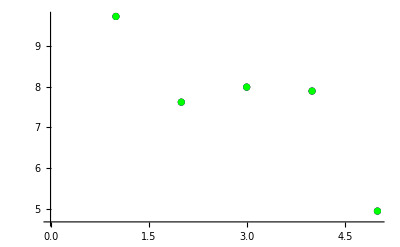

```mathematica
ListPlot[𝓋⟦1;;3⟧,PlotStyle->colors]
```

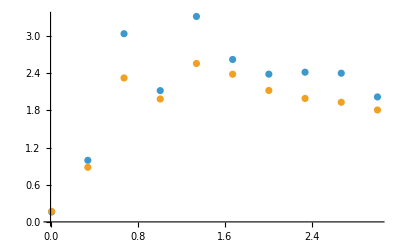

```mathematica
{{Ts[[1;;10]],-(asym[[21;;30]]-asym[[1;;10]])}//Transpose,{Ts[[1;;10]],-(asym[[31;;40]]-asym[[11;;20]])}//Transpose}//ListPlot
```

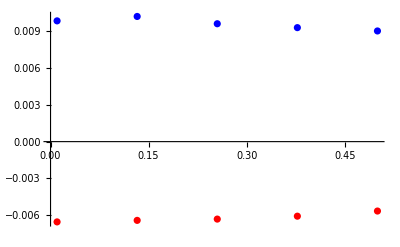

```mathematica
ListPlot[{Table[{annuluswidth⟦i⟧,asym⟦i⟧},{i,nsim2/2}],Table[{annuluswidth⟦i⟧,-(R0[[i]] asym⟦nsim2/2+i⟧-asym⟦i⟧)/Lns⟦i+nsim2/2⟧},{i,nsim2/2}]},PlotStyle->{Red,Blue}]
```

```mathematica
DQas
```

{3.66786,3.4849,3.36695,3.36116,3.13308,3.76704,3.56778,3.83493,3.17454,2.64026}

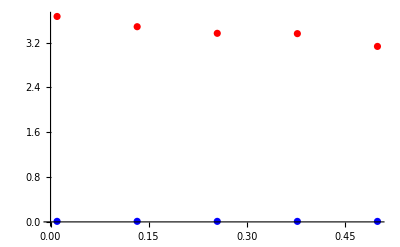

```mathematica
ListPlot[{Table[{annuluswidth⟦i⟧,DQas⟦i⟧},{i,nsim2/2}],Table[{annuluswidth⟦i⟧,-(R0[[i]] asym⟦nsim2/2+i⟧-asym⟦i⟧)/Lns⟦i+nsim2/2⟧},{i,nsim2/2}]},PlotStyle->{Red,Blue}]
```

```mathematica
ListPlot[{Table[{Ts⟦i⟧,asym⟦i⟧},{i,10}],Table[{Ts⟦i⟧,-(R0[[i]] asym⟦10+i⟧-asym⟦i⟧)/Lns⟦i+10⟧},{i,nsim2/2}]},PlotStyle->{Red,Blue}]
```

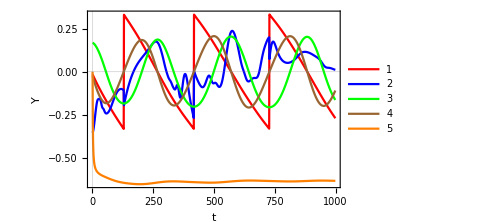

```mathematica
as=5;{init,fin}={2,Nt[[1]]};graftime[{θ⟦as,1,1,2,init;;fin⟧/π/3,ck2[[as,1,1,2,init;;fin]],X[[as,1,1,2,init;;fin]]-1,Y[[as,1,1,2,init;;fin]],(Z[[as,1,1,2,init;;fin]]-Z[[as,1,1,2,init]])/t[[as,init;;fin]]},"Y"]
```

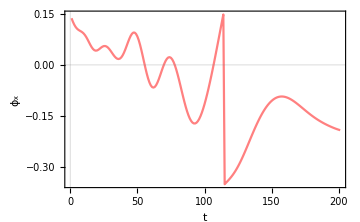

```mathematica
,graftime[,"ϕ_x"]
```

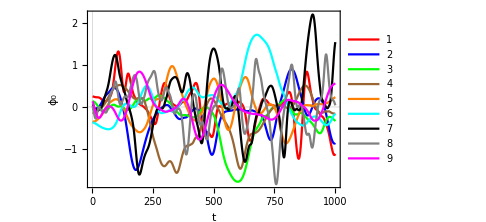
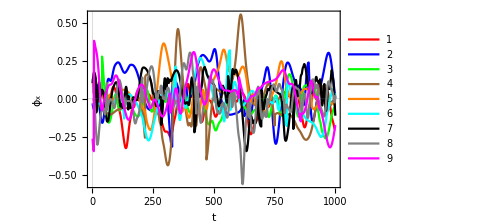
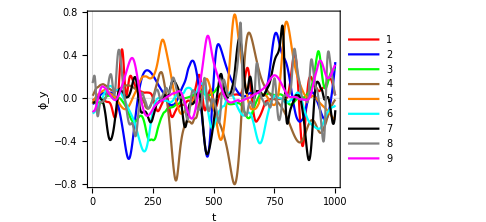

```mathematica
as=5;{graftime[ck1⟦as,1,1,2;;10⟧,"ϕ_0"],graftime[ck2⟦as,1,1,2;;10⟧,"ϕ_x"],graftime[ck3⟦as,1,1,2;;10⟧,"ϕ_y"]}
```

```mathematica
(*E o discontinuitate in phix....E normala, se compenseaza cu g(i,j) care si ele au discontinuitati; totul se trage de fapt de la lipsa periodicitatii pui ∂_x *care nu e acelasi lucru cu discontinuitatea gradientului; drept dovada, traiectoriile sunt continue*)
```

```mathematica
(∫_0^(2 π) Cos[θ3]^3 (1+ϵ Cos[θ3])ⅆθ3)/(∫_0^(2 π) Cos[θ3]^0 (1+ϵ Cos[θ3])ⅆθ3)
```

(3 ϵ)/8

```mathematica
(*checking the weight loading*)
```

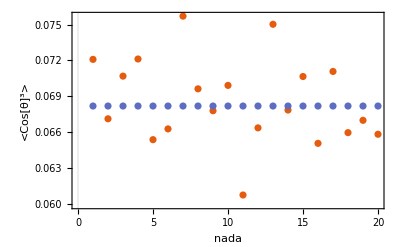

```mathematica
as=1;θ=ArcTan[Xallin-1,Yallin];guess=Integrate[Cos[θ2]^3(1+ϵ Cos[θ2]),{θ2,0,2π},{ξ2,0,2π}]/Integrate[(1+ϵ Cos[θ2]),{θ2,0,2π},{ξ2,0,2π}]/.ϵ->r00;
ListPlot[{Mean[Transpose[Cos[θ]^3 Pballin]],(Range[nsim2]0+1)guess},PlotTheme->"Scientific",FrameLabel->{"nada","<Cos[θ]^3>"}]
```

{{2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

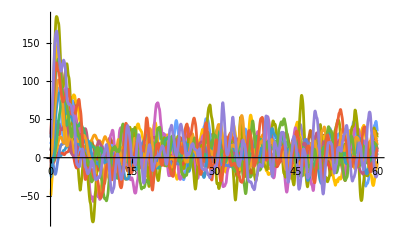
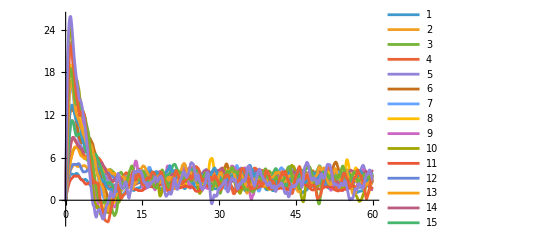

```mathematica
{turbmodel,USEturb,USElarmor,USEtilt,USEballoon,USEfreq,USEpolar}
{ListLinePlot[VQ1,PlotRange->All],ListLinePlot[DQ1,PlotRange->All,PlotLegends->Automatic]}
```

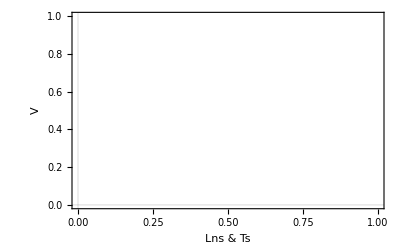
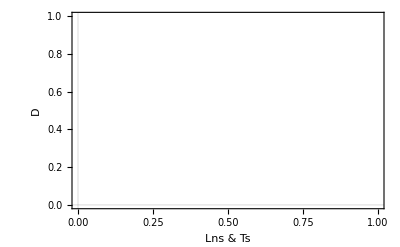

```mathematica
i=1;{ListPlot[{Transpose[{esence⟦i,2⟧,esence⟦i,3⟧}]},PlotTheme->"Scientific",FrameLabel->{esence[[i,1]],"V"},PlotRange->All],ListPlot[{Transpose[{esence⟦i,2⟧,esence⟦i,4⟧}]},PlotTheme->"Scientific",FrameLabel->{esence[[i,1]],"D"},PlotRange->All]}
```

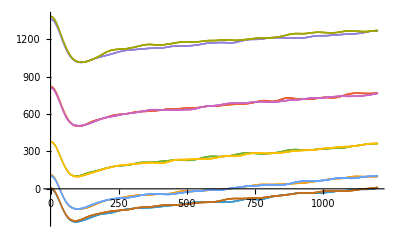

```mathematica
Q2GF-Q1GF^2//ListPlot
```

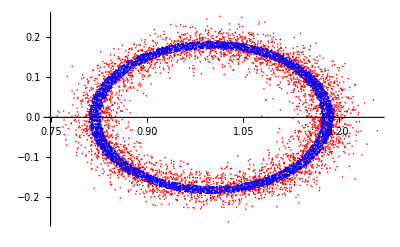
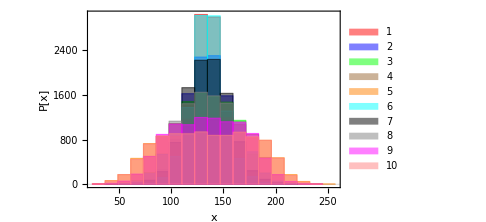
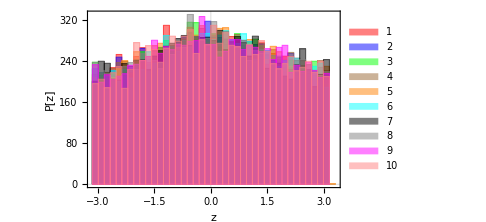
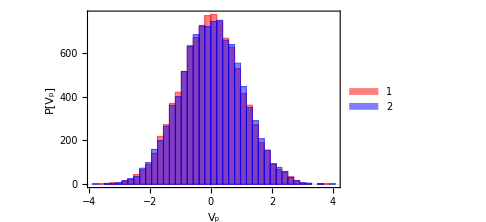

{0,0,1.28653}

```mathematica
as=1;nmax=5 10^3;θ=ArcTan[Xallout-1,Yallout];{ListPlot[{Transpose[{Xallout⟦as,1;;nmax⟧,Yallout⟦as,1;;nmax⟧}],Transpose[{Xallin⟦as,1;;nmax⟧,Yallin⟦as,1;;nmax⟧}]},PlotRange->All,PlotStyle->{Red,Blue}],histo[q1allout[[1;;nsim2]],"x"],histo[θ,"z"],histo[{Vpallin⟦as⟧,Vpallout⟦as⟧},"V_p"]}
{Count[Flatten[kz],Indeterminate],kperp//Max,X//Max}
```

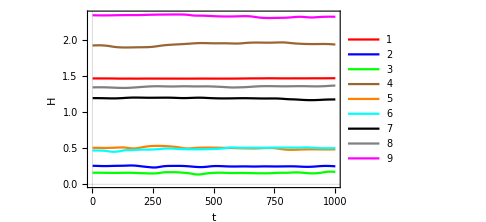
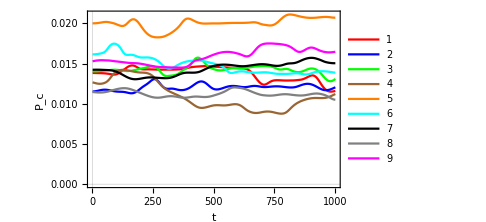
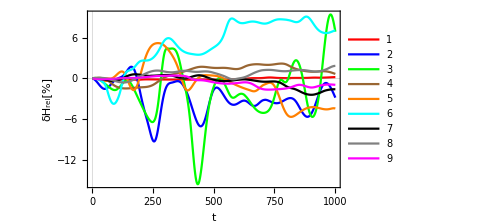
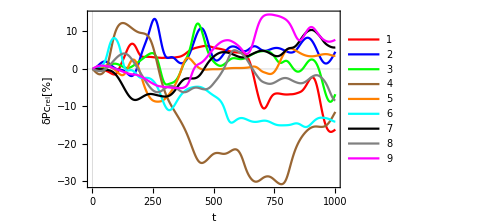

```mathematica
as=2;{graftime[H⟦as,1,1,2;;10⟧,"H"],graftime[Pc⟦as,1,1,2;;10⟧,"P_c"],graftime[(H⟦as,1,1,2;;10⟧/H⟦as,1,1,2;;10,1⟧-1) 10^2,"δH_rel[%]"],graftime[(Pc⟦as,1,1,2;;10⟧/Pc⟦as,1,1,2;;10,1⟧-1) 10^2,"δPc_rel[%]"]}
```

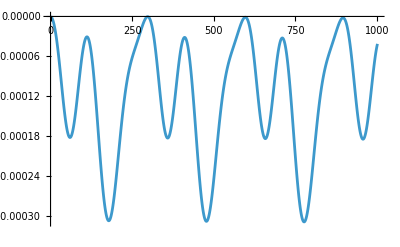

```mathematica
10000(Pc[[1,1,1,1]]/Pc[[1,1,1,1,1]]-1)//ListLinePlot
```

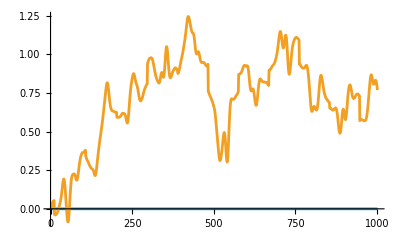

```mathematica
1000(H[[1,1,1,1;;2]]/H[[1,1,1,1;;2,1]]-1)//ListLinePlot
```

```mathematica
(Phi^2 tauc)/lambday^2
```

{0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005}

```mathematica
{Xallout[[as]],Yallout[[as]],weallin[[as]]}//Transpose//ListPointPlot3D
```

-Graphics3D-

$Aborted

```mathematica
(*Eu zic ca pe cazul asta se poate calcula analitic si aflu odata de ce e pe crestere pozitiva*)
```

```mathematica
(*Deci:
T=0; point-like distribution;

1. OLD;
- θ=0 :: V<0  (and stays like that);
- θ=π/2 :: V<0;
- θ=-π/2 :: V<0;
- θ=π :: V>0, very large and lack of energy conservation; all due to discontinuities; this explains the overall positive pinch;


2. OLD + tilt
- θ=0 :: V<0 altough some strange shape of the dkistribution of particles;
- θ=π/2 :: V<0;
- θ=-π/2 :: V<0;
- θ=π :: V<0,  energy conservation corrected;


3. NEW 
- θ=0 :: V<¬0 ; but keep in mind the problem of too large lbalonz which poses numerical problems;
- the same is confirmed for all other points; but it might be due to a too large lbalonz? 


4. NEW+ lower balonz;
- θ=0 :: V<0  ;
- θ=π/2 :: V>0  ;
- θ=-π/2 :: V>0;
- θ=π :: V>0;
-θ=0.8π:: V>0;

very strange indeed: at θ=0 there is negative pinch, positive in rest;lets try another point: i did, there are no inherently special things;
also, lbalonz does not change the sign. so i also dont know if its from the parallel structure (which includes tilting) or not;

--------;
-this is not an explanation why the pinch appears, where is the negative acceleration coming from;
-one problem is: how to make a simple turbulent model that has only x,y dependencies, but is also globally periodic?;
-this might be the whole problem: the turbulence models are shit; they might not be so shity for diffusion, but, aparently, the pinch is a very sensitive effect;

*)
```

```mathematica
(*E foarte ciudat cu *)
```

```mathematica
(*ar putea fi de la niste particule nereprezentate corect?*)
```

```mathematica
R0/LT
```

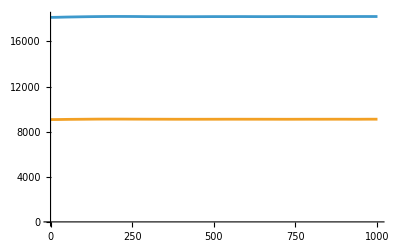
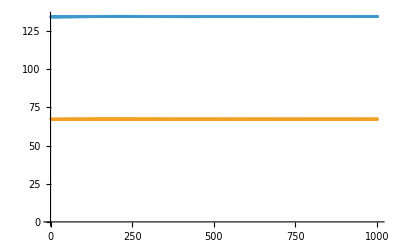
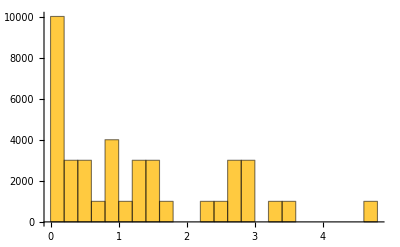

```mathematica
{ListLinePlot[𝓆2,PlotRange->All,ImageSize->400],ListPlot[𝓆1,PlotRange->All,ImageSize->400],Histogram[Flatten[H]]}
```

```mathematica
(*faptul ca viteza pleaca de la 0, imi spune mie ca e un proces de accelerare, ceea ce ar exclude gradB? poate doar compresie paralela? dar de unde?*)
```

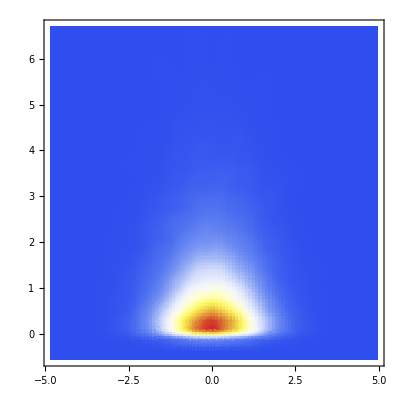

-Graphics-

```mathematica
as=1;pp[aa_,bb_]=PDF[SmoothKernelDistribution[Transpose[{Vpallin⟦as⟧,muallin⟦as⟧}]],{aa,bb}];limits={{pp[aa,bb][[1,1,2,1,2]],pp[aa,bb][[1,1,2,3,2]]},{pp[aa,bb][[1,1,2,2,2]],pp[aa,bb][[1,1,2,4,2]]}};DensityPlot[pp[aa,bb],{aa,limits[[1,1]],limits[[1,2]]},{bb,limits[[2,1]],limits[[2,2]]/2},PlotPoints->100,PlotRange->All,ColorFunction->"TemperatureMap"]
pp[aa_,bb_]=PDF[SmoothKernelDistribution[Transpose[{Vpallout⟦as⟧,muallout⟦as⟧}]],{aa,bb}];limits={{pp[aa,bb][[1,1,2,1,2]],pp[aa,bb][[1,1,2,3,2]]},{pp[aa,bb][[1,1,2,2,2]],pp[aa,bb][[1,1,2,4,2]]}};DensityPlot[pp[aa,bb],{aa,limits[[1,1]],limits[[1,2]]},{bb,limits[[2,1]],limits[[2,2]]/2},PlotPoints->100,PlotRange->All,ColorFunction->"TemperatureMap"]
```

```mathematica
whc=2;os=6;
{ListLinePlot[Transpose[{q1⟦os,1,1,whc⟧,q2⟦os,1,1,whc⟧}],PlotRange->All,FrameLabel->{"x","y"},PlotTheme->"Scientific"],ListLinePlot[Transpose[{X⟦os,1,1,whc⟧,Y⟦os,1,1,whc⟧}],PlotRange->All,FrameLabel->{"R","Z"},PlotTheme->"Scientific"],ListLinePlot[Transpose[{q2⟦os,1,1,whc⟧,q3⟦os,1,1,whc⟧}],PlotRange->All,FrameLabel->{"z","y"},PlotTheme->"Scientific"]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
as1=1;as2=2;whc=4;
{ListLinePlot[{q1⟦as1,1,1,1⟧,q1⟦as2,1,1,1⟧}],ListLinePlot[{q2⟦as1,1,1,1⟧,-q2⟦as2,1,1,1⟧}],ListLinePlot[{q3⟦as1,1,1,1⟧,-q3⟦as2,1,1,1⟧}]}
{ListLinePlot[{q1⟦as1,1,1,whc⟧,q1⟦as2,1,1,whc⟧}],ListLinePlot[{q2⟦as1,1,1,whc⟧,-q2⟦as2,1,1,whc⟧}],ListLinePlot[{q3⟦as1,1,1,whc⟧,-q3⟦as2,1,1,whc⟧}]}
```

{-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ListLinePlot[{X⟦as1,1,1,1⟧,X⟦as2,1,1,1⟧}],ListLinePlot[{Y⟦as1,1,1,1⟧,-Y⟦as2,1,1,1⟧}],ListLinePlot[{Z⟦as1,1,1,1⟧,-Z⟦as2,1,1,1⟧}],ListLinePlot[X⟦as1,1,1,1⟧-X⟦as2,1,1,1⟧],ListLinePlot[Y⟦as1,1,1,1⟧+Y⟦as2,1,1,1⟧],ListLinePlot[Z⟦as1,1,1,1⟧+Z⟦as2,1,1,1⟧]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Testing neoclassical motion in the circular geometry*)
```

```mathematica
{as,real,loop,part}={1,1,1,7};η=0.000001;θ=ArcTan[X-1,Y];
qsafe=Table[s1[[as]]+s2[[as]] (ρ[[as]]/a0[[as]])+s3[[as]](ρ[[as]]/a0[[as]])^2,{as,nsim2}];β=ρ/Sqrt[1-ρ^2]/qsafe;B= Sqrt[1+β^2]/(1+ρ Cos[θ]);
ρ0=Sqrt[(Xallin-1)^2+Yallin^2];β0=Table[ρ0[[as]]/q00[[as]]/Sqrt[1-ρ0[[as]]^2],{as,nsim2}];Bmin0=Table[Sqrt[1+(β0[[as]])^2]/(1+ρ0[[as]]),{as,nsim2}];
Bmax0=Table[Sqrt[1+(β0[[as]])^2]/(1-ρ0[[as]]),{as,nsim2}];
Bmax=Sqrt[1+(β)^2]/(1-ρ);
θ0=ArcTan[Xallin-1,Yallin];
```

```mathematica
exacttraped=Sqrt[ρ0(1+Cos[θ0])/(1+ρ0 Cos[θ0])]Pb;exacttraped=exacttraped[[All,1;;ntraj[[1]]]];
exacttraped=exacttraped//Transpose//Mean;ccc=Vpallin^2/2+muallin Sqrt[1+β0^2]/(1+ρ0 Cos[θ0])-muallin Bmax0;
```

```mathematica
nmax=10;{ListLinePlot[(H/((+Vp^2)/2+μ B))⟦as,1,1,1;;nmax⟧-1,PlotRange->All,PlotLabel->{"Correct energy"},FrameLabel->{"t","E/(mvp^2/2+μ B)"},PlotTheme->"Scientific"],ListLinePlot[H⟦as,1,1,1;;nmax⟧/H⟦as,1,1,1;;nmax,1⟧-1,PlotRange->All,PlotLabel->{"energy conservation"},FrameLabel->{"t","E/E(0)-1"},PlotTheme->"Scientific"],ListLinePlot[{1/(((H/(μ B))⟦as,real,loop,part⟧-1)^2+η),1/((Vp⟦as,real,loop,part⟧)^2+η)},PlotRange->All,PlotTheme->"Scientific",PlotLabel->"Mirror condition",FrameLabel->{"t","δ(mirror),δ(vp)"}]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{as,real,loop}={1,1,1};
hasSignChange[v_]:=Boole[Min[v RotateLeft[v]]<0]
class1=N[Mean]/@Table[hasSignChange/@Vp⟦as,real,loop⟧,{as,nsim2}]//N;
class2=Table[hasSignChange/@Vp⟦as,real,loop⟧,{as,nsim2}]//N;
class3=Table[Boole[H[[as,real,loop,part,1]]<μ[[as,real,loop,part,1]]*Bmax[[as,real,loop,part,1]]],{as,nsim2},{part,ntraj[[1]]}];
```

```mathematica
as=1;{{Vp[[as,real,loop,All,1]],μ[[as,real,loop,All,1]],class2[[as]]}//Transpose,{Vp[[as,real,loop,All,1]],μ[[as,real,loop,All,1]],class3[[as]]}//Transpose}//ListPointPlot3D
```

-Graphics3D-

```mathematica
as=4;ListPointPlot3D[{Transpose[{H⟦as,real,loop,All,1⟧,μ⟦as,real,loop,All,1⟧,class2⟦as⟧}],Transpose[{H⟦as,real,loop,All,1⟧,μ⟦as,real,loop,All,1⟧,class3⟦as⟧}]},PlotTheme->"Scientific",AxesLabel->{"E","μ","class"}]
```

Part::partw: Part 4 of «1» does not exist.

Part::partw: Part 4 of {{{{{0.472918,0.472918,0.472918,0.472918,0.472918,0.472918,0.472918,0.472918,0.472918,0.472918,0.472918,0.472918,0.472918,0.472918,0.472918,«21»,0.472918,0.472918,0.472918,0.472918,0.472918,0.472918,0.472918,0.472918,0.472918,0.472918,0.472918,0.472918,0.472918,0.472918,«951»},«8»,{«19»,«49»,«951»}}}},«1»} does not exist.

Part::partw: Part 4 of {{0.,0.,0.,0.,0.,0.,1.,0.,1.,1.},{0.,1.,1.,1.,1.,0.,1.,0.,0.,0.}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics3D-

```mathematica
{(0.9Sqrt[r00])^2,(class1)^2,(Pb[[All,1;;Length[class3[[1]]]]]class3//Transpose//Mean)^2}//ListPlot
```

-Graphics-

```mathematica
ListLinePlot[{exacttraped^2,class1^2,Mean[Transpose[Pb⟦All,1;;Length[class3⟦1⟧]⟧ class3]]^2},PlotMarkers->Automatic]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
ListLinePlot[Table[Count[HeavisideTheta[Vp⟦as,real,loop,part⟧ RotateLeft[Vp⟦as,real,loop,part⟧]],0],{part,ntraj⟦1⟧,ntraj⟦1⟧}]]
```

ListLinePlot::lpn: 0 is not a list of numbers or pairs of numbers.

ListLinePlot[0]

```mathematica
gradB={{(B0^2 (a0^4 R0 r00^2+(1+r00) (R0-R0 r00) (a0^2 safe1+a0 r00 safe2+r00^2 safe3)^2+(a0^4 R0 (a0^2 safe1+a0 r00^3 safe2+r00^2 (-1+2 r00^2) safe3) (-1+X0) X0)/((-1+r00^2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3))))/((a0^4 (-safe1^2+r00^2 (-1+safe1^2))+2 a0^3 r00 (-1+r00^2) safe1 safe2+2 a0 r00^3 (-1+r00^2) safe2 safe3+r00^4 (-1+r00^2) safe3^2+a0^2 r00^2 (-1+r00^2) (safe2^2+2 safe1 safe3)) X0),(a0^4 B0^2 R0 (a0^2 safe1+a0 r00^3 safe2+r00^2 (-1+2 r00^2) safe3) Y0)/((-1+r00) (1+r00) (a0^2 safe1+a0 r00 safe2+r00^2 safe3) (a0^4 (-safe1^2+r00^2 (-1+safe1^2))+2 a0^3 r00 (-1+r00^2) safe1 safe2+2 a0 r00^3 (-1+r00^2) safe2 safe3+r00^4 (-1+r00^2) safe3^2+a0^2 r00^2 (-1+r00^2) (safe2^2+2 safe1 safe3)))},{-((a0^4 B0^2 R0 (a0^2 safe1+a0 r00^3 safe2+r00^2 (-1+2 r00^2) safe3) Y0)/((-1+r00^2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3) (a0^4 (-safe1^2+r00^2 (-1+safe1^2))+2 a0^3 r00 (-1+r00^2) safe1 safe2+2 a0 r00^3 (-1+r00^2) safe2 safe3+r00^4 (-1+r00^2) safe3^2+a0^2 r00^2 (-1+r00^2) (safe2^2+2 safe1 safe3)) √((1-(a0^4 r00^2)/((-1+r00^2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3)^2))/X0^2) X0)),-(B0^2 R0 (1-(a0^4 (-1+X0)^2)/((-1+r00^2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3)^2)-(a0^4 (a0^2 safe1+a0 r00^3 safe2+r00^2 (-1+2 r00^2) safe3) (-1+X0) X0)/((-1+r00^2)^2 (a0^2 safe1+a0 r00 safe2+r00^2 safe3)^3)-(a0^4 Y0^2)/((-1+r00^2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3)^2)))/(((1-(a0^4 r00^2)/((-1+r00^2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3)^2))/X0^2)^(3/2) X0^4),-((a0^2 B0^2 (a0^4 (2 safe1^2-r00^2 (-1+safe1^2))-a0^3 r00 (-3+r00^2) safe1 safe2+a0 r00^3 (1+r00^2) safe2 safe3+r00^6 safe3^2+a0^2 r00^2 (safe2^2+2 safe1 safe3)))/(√(1-r00^2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3) (a0^4 (-safe1^2+r00^2 (-1+safe1^2))+2 a0^3 r00 (-1+r00^2) safe1 safe2+2 a0 r00^3 (-1+r00^2) safe2 safe3+r00^4 (-1+r00^2) safe3^2+a0^2 r00^2 (-1+r00^2) (safe2^2+2 safe1 safe3)) √((1-(a0^4 r00^2)/((-1+r00^2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3)^2))/X0^2) X0^2))}};
```

```mathematica
{gradB,rotB}={gradB⟦1⟧,gradB⟦2⟧};
```

```mathematica
{psir,psiz,psirr,psirz,psizz}={(a0^2 R0 (-1+X0))/(√(-R0^2 (-1+r00^2)) (a0^2 safe1+a0 r00 safe2+r00^2 safe3)),(a0^2 R0 Y0)/(√(-R0^2 (-1+r00^2)) (a0^2 safe1+a0 r00 safe2+r00^2 safe3)),-(a0^2 R0^2 (-((a0^2 safe1+a0 r00^3 safe2+r00^2 (-1+2 r00^2) safe3) (-1+X0)^2)+(-1+r00^2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3) Y0^2))/((-R0^2 (-1+r00^2))^(3/2) (a0 r00 (a0 safe1+r00 safe2)+r00^3 safe3)^2),(a0^2 R0^2 (a0^2 r00 safe1+a0 (-1+2 r00^2) safe2+r00 (-2+3 r00^2) safe3) (-1+X0) Y0)/(r00 (-R0^2 (-1+r00^2))^(3/2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3)^2),-(a0^2 R0^2 ((-1+r00^2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3) (-1+X0)^2-(a0^2 safe1+a0 r00^3 safe2+r00^2 (-1+2 r00^2) safe3) Y0^2))/((-R0^2 (-1+r00^2))^(3/2) (a0 r00 (a0 safe1+r00 safe2)+r00^3 safe3)^2)};
```

```mathematica
{ListPlot[{gradB⟦1⟧,q1⟦All,1,1,1,1⟧},AxesLabel->{"","gradBx"}],ListPlot[{gradB⟦2⟧,q2⟦All,1,1,1,1⟧},AxesLabel->{"","gradBy"}],ListPlot[{rotB⟦1⟧,q3⟦All,1,1,1,1⟧},AxesLabel->{"","rotBx"}],ListPlot[{rotB⟦2⟧,H⟦All,1,1,1,1⟧},AxesLabel->{"","gradBy"}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ListPlot[{psir R0,q3⟦All,1,1,1,1⟧},AxesLabel->{"","rotBx"}],ListPlot[{R0 psiz,H⟦All,1,1,1,1⟧},AxesLabel->{"","gradBy"}]}
```

{-Graphics-,-Graphics-}

```mathematica
ListLinePlot[q3⟦as1,1,1,1⟧+q3⟦as2,1,1,1⟧]
```

-Graphics-

```mathematica
ListPlot[{lambdaz,DQas}//Transpose,PlotRange->All]
```

-Graphics-

```mathematica
max=Nt[[1]];sa=4;da=1;{ListPlot[Transpose[{X⟦1,1,da,sa,1;;max⟧,Y⟦1,1,da,sa,1;;max⟧}]],ListPlot[Vp⟦1,1,da,sa,1;;max⟧],ListPlot[Z⟦1,1,da,sa,1;;max⟧],ListPlot[ρ⟦1,1,da,sa,1;;max⟧]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Monitor[For[i=1,i≤nsim2,i++,For[j=1,j≤Nloop⟦i⟧,j++,Subscript[trajx, i,j]=Interpolation[Transpose[{t⟦i⟧,x⟦i,1,j,2⟧}]];Subscript[trajy, i,j]=Interpolation[Transpose[{t⟦i⟧,y⟦i,1,j,2⟧}]];Subscript[trajz, i,j]=Interpolation[Transpose[{t⟦i⟧,z⟦i,1,j,2⟧}]];]],{i,j}]
```

```mathematica
torus[u_,v_,R_:1,r_:a0⟦1⟧]:={(R+r Cos[v]) Cos[u],(R+r Cos[v]) Sin[u],r Sin[v]};
limits={{-(1+a0⟦1⟧),1+a0⟦1⟧},{-(1+a0⟦1⟧),1+a0⟦1⟧},{-a0⟦1⟧,a0⟦1⟧}};
torusSurface=ParametricPlot3D[torus[u,v],{u,0,3π/2},{v,0,2π},Mesh->None,PlotStyle->Directive[Opacity[0.4],ColorFunction->"TemperatureMap",Specularity[White,50]],Lighting->"Neutral",ColorFunctionScaling->True];
{i,j}={1,3};
colors={{Red},{Blue},{Green},{Orange},{Pink},{Magenta},{Cyan},{Black},{Brown},{Gray}};
colors=Black;trajs=Table[{Subscript[trajx, i,j][τ],Subscript[trajy, i,j][τ],Subscript[trajz, i,j][τ]},{j,Nloop⟦1⟧}];trajs=ParametricPlot3D[{trajs⟦1⟧,trajs⟦2⟧,trajs⟦3⟧},{τ,0,14+0 tmax⟦1⟧},PlotRange->limits,PlotStyle->{Hue[0.58]}];
Show[trajs,torusSurface,Boxed->False,Axes->False,ImageSize->Large]
```

Part::partw: Part 3 of {{0.938982,0.450778,0.17653},{0.328572,-0.808367,0.129352}} does not exist.

Part::partw: Part 3 of {{1.08789,0.0745278,0.154994},{0.6157,-0.575548,0.0893572}} does not exist.

Part::partw: Part 3 of {{1.07993,-0.340448,0.119054},{0.784559,-0.255264,0.0437352}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics3D-

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of {{0.0706198,-0.919626,0.0211687}} does not exist.

Part::partw: Part 2 of {{-0.381717,-0.841233,0.000369373}} does not exist.

Part::partw: Part 2 of {{-0.7436,-0.557572,-0.0196391}} does not exist.

Part::partw: Part 2 of {{trajx_(2,1)[0.000286],trajy_(2,1)[0.000286],trajz_(2,1)[0.000286]}} does not exist.

Part::partw: Part 2 of {{trajx_(2,1)[0.286],trajy_(2,1)[0.286],trajz_(2,1)[0.286]}} does not exist.

Part::partw: Part 2 of {{trajx_(2,1)[0.571715],trajy_(2,1)[0.571715],trajz_(2,1)[0.571715]}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Monitor[For[i=1,i≤nsim2,i++,For[j=1,j≤Nloop⟦i⟧,j++,Subscript[trajx, i,j]=Interpolation[Transpose[{t⟦i⟧,X⟦i,1,j,2⟧}]];Subscript[trajy, i,j]=Interpolation[Transpose[{t⟦i⟧,Y⟦i,1,j,2⟧}]];]],{i,j}]
```

```mathematica
{i,j}={1,3};Show[ParametricPlot[Table[{Subscript[trajx, i,j][τ],Subscript[trajy, i,j][τ]},{j,Nloop⟦1⟧}],{τ,0,14+0 tmax⟦1⟧},PlotRange->{{0.6,1.4},{-.4,.4}}],Graphics[{Red,Circle[{1,0},a0⟦1⟧]}]]
```

-Graphics-

```mathematica
ParametricPlot[Table[{Subscript[trajx, i,j][τ],Subscript[trajy, i,j][τ]},{j,Nloop[[1]]}],{τ,0,4+0tmax[[1]]},PlotRange->{{0.7,1.3},{-.3,.3}}]
```

-Graphics-

```mathematica
{{q1[[1,1,1,1]],q2[[1,1,1,1]]}//Transpose//ListPlot,q1[[1,1,1,1]]//ListPlot,q2[[1,1,1,1]]//ListPlot,{X[[1,1,1,1]],Y[[1,1,1,1]]}//Transpose//ListPlot}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Λ0=1/2 Table[HeavisideTheta[i-j-0.01]+HeavisideTheta[i-j+0.01],{i,Nt⟦1⟧+1},{j,Nt⟦1⟧+1}];Λ0⟦All,1⟧=1/2;Λ0⟦1,1⟧=0;
Λ=(R0⟦1⟧ dt⟦1⟧ Λ0)/vth⟦1⟧;
```

```mathematica
as=1;{kz[[as]],kperp[[as]]}//Transpose//ListPlot
as=9;{kz[[as]],kperp[[as]]}//Transpose//ListPlot
```

```mathematica
DQ1//ListPlot
```

-Graphics-

```mathematica
ListPlot[DQ1,PlotRange->All]
```

-Graphics-

```mathematica
fact=1.0;neo=Table[Sqrt[(kz[[as]]-1)^2+kperp[[as]]^2],{as,1,2}]/a0[[1]]/fact//Flatten;
coll=Table[Sqrt[(kz[[as]]-1)^2+kperp[[as]]^2],{as,3,4}]/a0[[1]]/fact//Flatten;
turb=Table[Sqrt[(kz[[as]]-1)^2+kperp[[as]]^2],{as,5,6}]/a0[[1]]/fact//Flatten;
full=Table[Sqrt[(kz[[as]]-1)^2+kperp[[as]]^2],{as,7,8}]/a0[[1]]/fact//Flatten;
neo=neo-Mean[neo];
coll=coll-Mean[coll];
turb=turb-Mean[turb];
full=full-Mean[full];
```

Part::partw: Part 3 of {{0.139856,-0.14328,-0.187594,0.0245752,-0.166823,0.0874501,-0.181927,0.067053,-0.0836942,0.03165,-0.185014,0.138395,0.159406,-0.0537734,-0.0135886,-0.136251,-0.164288,-0.158686,«16»,-0.043998,-0.152344,0.0316431,-0.147691,0.0762724,0.064894,0.157854,0.196725,-0.157828,-0.00964634,-0.0831779,0.064175,0.191481,-0.163157,0.217674,-0.205034,«499950»},{«1»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

$Aborted

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of turb-Mean[turb].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of full-Mean[full].

```mathematica
legend=Grid[{{Graphics[{Gray,Disk[{0,0},0.1]},ImageSize->15],Style["neo",15,FontFamily->"Times New Roman"]},{Graphics[{Green,Disk[{0,0},0.1]},ImageSize->15],Style["coll",15,FontFamily->"Times New Roman"]},{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->15],Style["turb",15,FontFamily->"Times New Roman"]},{Graphics[{Red,Disk[{0,0},0.1]},ImageSize->15],Style["full",15,FontFamily->"Times New Roman"]}}];histo=Histogram[{neo,coll,turb,full},{0.01},PlotRange->All,ScalingFunctions->"Log",PlotTheme->"Scientific",LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,FrameLabel->{"r/a","P"},ChartStyle->{Gray,Green,Blue,Red},ChartLegends->Placed[legend,{0.8,0.8}]]
```

-Graphics-

```mathematica
legend=Grid[{{Graphics[{Gray,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_^(neo)",FontFamily->"Times New Roman",15,Bold]},{Graphics[{Green,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_^(col)",FontFamily->"Times New Roman",15,Bold]},
{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_^(turb)",FontFamily->"Times New Roman",15,Bold]},{Graphics[{Red,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_^(full)",FontFamily->"Times New Roman",15,Bold]},{Graphics[{Black,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_^(col)+𝒟_^(turb)",FontFamily->"Times New Roman",15,Bold]}}];
timecomp=ListLogLinearPlot[{Mean[DQ1⟦1;;2⟧],Mean[DQ1⟦3;;4⟧],Mean[DQ1⟦5;;6⟧],Mean[DQ1⟦7;;8⟧],{Mean[DQ1⟦3;;4,All,1⟧],Mean[DQ1⟦3;;4,All,2⟧]+Mean[DQ1⟦5;;6,All,2⟧]}//Transpose},PlotTheme->"Scientific",PlotRange->{{0,0.99Max[t]},{-0.3,4}},PlotLegends->Placed[legend,{0.15,0.75}],ImageSize->500,LabelStyle->{Black,Bold,18},PlotStyle->{Gray,Green,Blue,Red,Black},FrameLabel->{Style["t[R_0/v_th]",FontFamily->"Times New Roman",Bold],Style["𝒟_^(R)[m^2/s]",FontFamily->"Times New Roman",Bold]},Joined->True]
```

-Graphics-

```mathematica
legend=Grid[{{Graphics[{Red,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(turb - turb)^(turb)",FontFamily->"Times New Roman",15,Bold]},{Graphics[{Green,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(turb - turb)^(full)",FontFamily->"Times New Roman",15,Bold]},
{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(turb - turb)^(syn)",FontFamily->"Times New Roman",15,Bold]}}];
i=1;timecomp=ListLogLinearPlot[{Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorTT⟦5;;6⟧]]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorTT⟦7;;8⟧]]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorTT⟦7;;8⟧-VcorTT⟦5;;6⟧-VcorTT⟦3;;4⟧]]]}]},PlotTheme->"Scientific",PlotRange->{{0,0.99Max[t]},All},PlotLegends->Placed[legend,{0.15,0.75}],ImageSize->500,LabelStyle->{Black,Bold,18},PlotStyle->{Red,Green,Blue},FrameLabel->{Style["t[R_0/v_th]",FontFamily->"Times New Roman",Bold],Style["𝒟_^(R)[m^2/s]",FontFamily->"Times New Roman",Bold]},Joined->True]
```

-Graphics-

```mathematica
legend=Grid[{{Graphics[{Red,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(neo - neo)^(coll)",FontFamily->"Times New Roman",15,Bold]},{Graphics[{Green,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(neo - neo)^(full)",FontFamily->"Times New Roman",15,Bold]},
{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(neo - neo)^(syn)",FontFamily->"Times New Roman",15,Bold]}}];
i=1;timecomp=ListPlot[{Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorNN⟦3;;4⟧]]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorNN⟦7;;8⟧]]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorNN⟦7;;8⟧-VcorNN⟦3;;4⟧-VcorNN⟦5;;6⟧]]]}]},PlotTheme->"Scientific",PlotRange->{{0,0.99Max[t]},{-0.6,0.7}},PlotLegends->Placed[legend,{0.2,0.75}],ImageSize->500,LabelStyle->{Black,Bold,18},PlotStyle->{Red,Green,Blue},FrameLabel->{Style["t[R_0/v_th]",FontFamily->"Times New Roman",Bold],Style["𝒟_^(R)[m^2/s]",FontFamily->"Times New Roman",Bold]},Joined->True]
```

-Graphics-

```mathematica
legend=Grid[{{Graphics[{Red,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(neo - turb)^(turb)",FontFamily->"Times New Roman",15,Bold]},{Graphics[{Green,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(neo - turb)^(full)",FontFamily->"Times New Roman",15,Bold]},
{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(neo - turb)^(syn)",FontFamily->"Times New Roman",15,Bold]}}];
i=1;timecomp=ListPlot[{Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorNT⟦5;;6⟧]]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorNT⟦7;;8⟧]]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorNT⟦7;;8⟧-VcorNT⟦5;;6⟧-VcorNT⟦3;;4⟧]]]}]},PlotTheme->"Scientific",PlotRange->{{0,0.99Max[t]},All},PlotLegends->Placed[legend,{0.15,0.75}],ImageSize->500,LabelStyle->{Black,Bold,18},PlotStyle->{Red,Green,Blue},FrameLabel->{Style["t[R_0/v_th]",FontFamily->"Times New Roman",Bold],Style["𝒟_^(R)[m^2/s]",FontFamily->"Times New Roman",Bold]},Joined->True]
```

-Graphics-

```mathematica
legend=Grid[{{Graphics[{Red,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(turb - neo)^(turb)",FontFamily->"Times New Roman",15,Bold]},{Graphics[{Green,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(turb - neo)^(full)",FontFamily->"Times New Roman",15,Bold]},
{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(turb - neo)^(syn)",FontFamily->"Times New Roman",15,Bold]}}];
i=1;timecomp=ListPlot[{Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorTN⟦5;;6⟧]]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorTN⟦7;;8⟧]]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorTN⟦7;;8⟧-VcorTN⟦5;;6⟧-VcorTN⟦3;;4⟧]]]}]},PlotTheme->"Scientific",PlotRange->{{0,0.99Max[t]},All},PlotLegends->Placed[legend,{0.15,0.75}],ImageSize->500,LabelStyle->{Black,Bold,18},PlotStyle->{Red,Green,Blue},FrameLabel->{Style["t[R_0/v_th]",FontFamily->"Times New Roman",Bold],Style["𝒟_^(R)[m^2/s]",FontFamily->"Times New Roman",Bold]},Joined->True]
```

-Graphics-

```mathematica
i=2;{ListPlot[{Λ.VQ1⟦i,All,2⟧,rhoi[[i]](𝓆1[[i]]-𝓆1[[i,1]])}],ListPlot[{Λ.DQ1[[i,All,2]],1/2 rhoi[[i]]^2(𝓆2[[i]]-𝓆1[[i]]^2)},PlotRange->All]}
```

{-Graphics-,-Graphics-}

```mathematica
i=8;{ListPlot[{Λ.(vth⟦i⟧ Mean[Mean[VT⟦i⟧+V0⟦i⟧]]),Λ.VQ1⟦i,All,2⟧,rhoi⟦1⟧ (𝓆1⟦i⟧-𝓆1⟦i,1⟧)},PlotRange->{{0,999},Automatic}],ListPlot[{Λ.(vth⟦i⟧ Mean[Mean[VT⟦i⟧+V0⟦i⟧]])-Λ.VQ1⟦i,All,2⟧},PlotRange->{{0,999},Automatic}]}
```

{-Graphics-,-Graphics-}

```mathematica
i=2;ListLinePlot[{Λ.Mean[Mean[vth⟦i⟧ V0⟦i⟧]],Λ.Mean[Mean[vth⟦i⟧ VT⟦i⟧]],vth⟦i⟧ Λ.Mean[Mean[V0⟦i⟧+VT⟦i⟧]],rhoi⟦1⟧ (Mean[Mean[Q1⟦i⟧]]-Mean[Mean[Q1⟦i⟧]][[1]])},PlotStyle->{Red,Blue,Green,Orange},PlotLegends->Placed[{"Neo","Turb","full","real"},{1.,.6}],PlotRange->All,ImageSize->400]
```

-Graphics-

```mathematica
i=8;{t1,t2}={400,712};{ListPlot[{Vcorff⟦i,t1⟧,RotateLeft[Vcorff⟦i,t2⟧,-(t1-t2)]},PlotRange->All],ListPlot[{VcorNT⟦i,t1⟧,RotateLeft[VcorNT⟦i,t2⟧,-(t1-t2)]},PlotRange->All],ListPlot[{VcorTN⟦i,t1⟧,RotateLeft[VcorTN⟦i,t2⟧,-(t1-t2)]},PlotRange->All],ListPlot[{VcorTT⟦i,t1⟧,RotateLeft[VcorTT⟦i,t2⟧,-(t1-t2)]},PlotRange->All],ListPlot[{VcorNN⟦i,t1⟧,RotateLeft[VcorNN⟦i,t2⟧,-(t1-t2)]},PlotRange->All]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[Transpose[{nub,DQas}],PlotTheme->"Scientific",PlotRange->All,ImageSize->500,LabelStyle->{Black,Bold,18},PlotStyle->{Red,Green,Blue},FrameLabel->{Style["ν^*",FontFamily->"Times New Roman",Bold],Style["𝒟_^(coll)[m^2/s]",FontFamily->"Times New Roman",Bold]},Joined->True,PlotMarkers->{Automatic,15}]
```

-Graphics-

```mathematica
ListPlot[Transpose[{100Phi,DQas}],PlotTheme->"Scientific",PlotRange->All,ImageSize->500,LabelStyle->{Black,Bold,18},PlotStyle->{Red,Green,Blue},FrameLabel->{Style["Φ [%]",FontFamily->"Times New Roman",Bold],Style["𝒟_^(turb)[m^2/s]",FontFamily->"Times New Roman",Bold]},Joined->True,PlotMarkers->{Automatic,15}]
```

-Graphics-

```mathematica
timecomp=ListPlot[{Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorNN⟦i⟧]]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorNN⟦7;;8⟧]]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorNN⟦7;;8⟧-VcorNN⟦3;;4⟧]]]}]},PlotTheme->"Scientific",PlotRange->{{0,0.99Max[t]},All},PlotLegends->Placed[legend,{0.15,0.75}],ImageSize->500,LabelStyle->{Black,Bold,18},PlotStyle->{Red,Green,Blue},FrameLabel->{Style["t[R_0/v_th]",FontFamily->"Times New Roman",Bold],Style["𝒟_^(R)[m^2/s]",FontFamily->"Times New Roman",Bold]},Joined->True]
```

-Graphics-

```mathematica
ListPlot[{Table[{10^2 Phi⟦i⟧,Mean[(Λ.Mean[Mean[LTT⟦i⟧]])⟦IntegerPart[(2 Nt⟦1⟧)/4];;Nt⟦1⟧⟧]},{i,nsim2}],Table[{10^2 Phi⟦i⟧,Mean[(Λ.Mean[Mean[L0T⟦i⟧]])⟦IntegerPart[(2 Nt⟦1⟧)/4];;Nt⟦1⟧⟧]},{i,nsim2}],Table[{10^2 Phi⟦i⟧,Mean[DQ1⟦i,IntegerPart[(2 Nt⟦1⟧)/3];;Nt⟦1⟧,2⟧]},{i,nsim2}]},Joined->True,PlotMarkers->{Automatic,22},PlotStyle->{Red,Blue,Green,Orange,Black},FrameLabel->{Style["Φ [%]",18,FontFamily->"Times New Roman"],Style["D [m^2/s]",18,FontFamily->"Times New Roman"]},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotLegends->Placed[{Style["D_turb^(turb)",FontFamily->"Times New Roman"],Style["D_neo^(turb)",FontFamily->"Times New Roman"],Style["D_^(turb)",FontFamily->"Times New Roman"]},{.2,.8}],PlotRange->All,PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
i=5;ListPlot[{Mean[Mean[LTT⟦i⟧]],VcorTT⟦i,1⟧,VcorTT⟦i,Nt[[1]]+1⟧//Reverse},PlotRange->{{0,140},All}]
```

-Graphics-

```mathematica
i=6;ListPlot[{DQ1[[i]],Transpose[{t⟦i⟧,vth⟦i⟧^2 Λ.Mean[Mean[LTT⟦i⟧+LT0⟦i⟧+L0T⟦i⟧+L00⟦i⟧]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Vcorff[[i]]]]}]},PlotRange->{All,5{-.1,.63}}]
```

-Graphics-

```mathematica
i=8;ListLinePlot[{{t[[i]],vth⟦i⟧^2 Λ.Mean[Mean[LTT⟦i⟧]]}//Transpose,{t[[i]],vth⟦i⟧^2 Λ.Mean[Mean[L0T⟦i⟧]]}//Transpose,{t[[i]],vth⟦i⟧^2 Λ.Mean[Mean[LT0⟦i⟧]]}//Transpose,{t[[i]],vth⟦i⟧^2 Λ.Mean[Mean[L00⟦i⟧]]}//Transpose,DQ1[[i]]},Joined->True,PlotStyle->{Red,Blue,Green,Orange,Black},PlotRange->{All,{-1,4}},FrameLabel->{Style["t [R_0/v_th]",18,FontFamily->"Times New Roman"],Style["D [m^2/s]",18,FontFamily->"Times New Roman"]},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotLegends->Placed[{Style["LTT",12,FontFamily->"Times New Roman"],Style["L0T",12,FontFamily->"Times New Roman"],Style["LT0",12,FontFamily->"Times New Roman"],Style["L00",12,FontFamily->"Times New Roman"],Style["𝒟",12,FontFamily->"Times New Roman"]},{0.9,.75}],PlotRange->All,PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
as=8;Sqrt[(1-kz[[as]])^2+kperp[[as]]^2]//Histogram
```

-Graphics-

```mathematica
{kz//Flatten,kperp//Flatten}//Transpose//ListPlot
```

-Graphics-

```mathematica
{{q1[[1,1,1,1]],q2[[1,1,1,1]]}//Transpose//ListPlot,q1[[1,1,1,1]]//ListPlot,q2[[1,1,1,1]]//ListPlot}
```

```mathematica
as=2;{kz[[as]],kperp[[as]]}//Transpose//ListPlot
```

-Graphics-

```mathematica
as=4;{kz[[as]],kperp[[as]]}//Transpose//ListPlot
```

-Graphics-

```mathematica
𝒟full=Interpolation[Transpose[{Phi,nub,DQas}]];
𝒟turb=Interpolation[Table[{Phi⟦20i+1⟧,DQas⟦20 i+1⟧},{i,0,9}]];
𝒟coll=Interpolation[Table[{nub⟦i⟧,DQas⟦i⟧},{i,1,20}]];
```

```mathematica
full=ArrayReshape[Table[{ϕ,ν,𝒟full[ϕ,ν]},{ϕ,Min[Phi],Max[Phi],1/40 (Max[Phi]-Min[Phi])},{ν,Min[nub],Max[nub],1/40 (Max[nub]-Min[nub])}],{1600,3}];
syn=ArrayReshape[Table[{ϕ,ν,𝒟full[ϕ,ν]-𝒟turb[ϕ]-𝒟coll[ν]},{ϕ,Min[Phi],Max[Phi],1/40 (Max[Phi]-Min[Phi])},{ν,Min[nub],Max[nub],1/40 (Max[nub]-Min[nub])}],{1600,3}];grafs1={ListPlot3D[full,PlotRange->All,PlotTheme->"Scientific",LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,AxesLabel->{"Φ","ν^*","𝒟^(full)"},ColorFunction->"TemperatureMap"],ListPlot3D[syn,PlotRange->All,PlotTheme->"Scientific",LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,AxesLabel->{"Φ","ν^*","𝒟^(syn)"},ColorFunction->"TemperatureMap"],ListPlot3D[ratio,PlotRange->{{0.002,Max[Phi]},{0.02,Max[nub]},{0,1}},PlotTheme->"Scientific",LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,AxesLabel->{"Φ","ν^*","D^(syn)/D^(turb)"},ColorFunction->"TemperatureMap"]}
```

```mathematica
{,,}
```

```mathematica
ratio=ArrayReshape[Table[{ϕ,ν,(𝒟full[ϕ,ν]-𝒟turb[ϕ]-𝒟coll[ν])/(Sqrt[𝒟turb[ϕ]𝒟coll[ν]]^2+0.00)},{ϕ,Min[Phi],Max[Phi],1/40 (Max[Phi]-Min[Phi])},{ν,Min[nub],Max[nub],1/40 (Max[nub]-Min[nub])}],{1600,3}];
ratio2={ratio[[All,1]],ratio[[All,2]],Mean[ratio[[All,3]]]+1.0(ratio[[All,3]]-Mean[ratio[[All,3]]])//Re}//Transpose;
hist=Histogram[ratio⟦All,3⟧,{0,1,0.05},PlotTheme->"Scientific",FrameLabel->{"𝒟^(syn)/𝒟^(turb)","P"},LabelStyle->{Black,Bold,20},ImageSize->500,ChartStyle->{Hue[.55]}]
```

-Graphics-

```mathematica
ratio1=ArrayReshape[Table[{ϕ,ν,(𝒟full[ϕ,ν]-𝒟turb[ϕ]-𝒟coll[ν])/(𝒟turb[ϕ])},{ϕ,Min[Phi],Max[Phi],1/40 (Max[Phi]-Min[Phi])},{ν,Min[nub],Max[nub],1/40 (Max[nub]-Min[nub])}],{1600,3}];
ratio2=ArrayReshape[Table[{ϕ,ν,(𝒟full[ϕ,ν]-𝒟turb[ϕ]-𝒟coll[ν])/(𝒟coll[ϕ])},{ϕ,Min[Phi],Max[Phi],1/40 (Max[Phi]-Min[Phi])},{ν,Min[nub],Max[nub],1/40 (Max[nub]-Min[nub])}],{1600,3}];
hist1=Histogram[ratio1⟦All,3⟧,{-.1,.3,0.01},PlotTheme->"Scientific",FrameLabel->{"𝒟^(syn)/𝒟^(turb)","P"},LabelStyle->{Black,Bold,20},ImageSize->500,ChartStyle->{Hue[.55]}]
hist2=Histogram[ratio2⟦All,3⟧,{-11.1,22.3,1},PlotTheme->"Scientific",FrameLabel->{"𝒟^(syn)/𝒟^(coll)","P"},LabelStyle->{Black,Bold,20},ImageSize->500,ChartStyle->{Hue[.55]}]
```

-Graphics-

-Graphics-

```mathematica
ratio[[All,3]]
```

```mathematica
hist=Histogram[GaussianFilter[ratio⟦All,3⟧,1],PlotTheme->"Scientific",FrameLabel->{"D^(syn)/D^(turb)","P"},LabelStyle->{Black,Bold,20},ImageSize->500,ChartStyle->Hue[.55]]
```

-Graphics-

```mathematica
syn//ListDensityPlot
```

```mathematica
graf2={ListPlot[Table[{ϕ,𝒟turb[ϕ]},{ϕ,0,Max[Phi],Max[Phi]/50}],PlotTheme->"Scientific",Joined->True,PlotMarkers->Automatic,LabelStyle->{Black,Bold,20},FrameLabel->{"Φ","𝒟^(turb)[m^2/s]"},ImageSize->500,PlotStyle->"TemperatureMap"],ListPlot[Table[{ν,𝒟coll[ν]},{ν,0,Max[nub],Max[nub]/50}],Joined->True,PlotMarkers->Automatic,PlotTheme->"Scientific",LabelStyle->{Black,Bold,20},FrameLabel->{"ν^*","𝒟^(coll)[m^2/s]"},ImageSize->500,PlotStyle->"TemperatureMap"]}
```

{-Graphics-,-Graphics-}

```mathematica
Export[expfoto<>"fig_1_a.eps",graf2[[1]]]
Export[expfoto<>"fig_1_b.eps",graf2[[2]]]
Export[expfoto<>"fig_2_a.eps",grafs1[[1]]]
Export[expfoto<>"fig_2_b.eps",grafs1[[2]]]
Export[expfoto<>"fig_2_c.eps",grafs1[[3]]]
Export[expfoto<>"fig_3.eps",hist]
```

F:\5_Plasma\2_Present\1_Neo_Turb_Synergies\Arxiv\fig_1_a.eps

F:\5_Plasma\2_Present\1_Neo_Turb_Synergies\Arxiv\fig_1_b.eps

F:\5_Plasma\2_Present\1_Neo_Turb_Synergies\Arxiv\fig_2_a.eps

F:\5_Plasma\2_Present\1_Neo_Turb_Synergies\Arxiv\fig_2_b.eps

F:\5_Plasma\2_Present\1_Neo_Turb_Synergies\Arxiv\fig_2_c.eps

F:\5_Plasma\2_Present\1_Neo_Turb_Synergies\Arxiv\fig_3.eps

-Graphics-

```mathematica
Export[expfoto<>"fig_4.eps",histo]
```

F:\5_Plasma\2_Present\1_Neo_Turb_Synergies\Arxiv\fig_4.eps

```mathematica
{size1,size2}={17,17};legend=Grid[{{Graphics[{Red,Disk[{0,0},0.1]},ImageSize->size1],Style["t = t_0",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->size1],Style["t = t_max",size2,FontFamily->"Times New Roman"]}}];fig1a=ListPlot[{Transpose[{kz[[1]]//Flatten,kperp[[1]]//Flatten}],Transpose[{kx[[1]]//Flatten,ky[[1]]//Flatten}]},PlotTheme->"Scientific",FrameLabel->{"R/R_0","Z/R_0"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotStyle->{Blue,Red},AspectRatio->Full,PlotLegends->Placed[legend,{0.85,0.08}]]
fig1b=ListPlot[{Transpose[{kz[[2]]//Flatten,kperp[[2]]//Flatten}],Transpose[{kx[[2]]//Flatten,ky[[2]]//Flatten}]},PlotTheme->"Scientific",FrameLabel->{"R/R_0","Z/R_0"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotStyle->{Blue,Red},AspectRatio->Full,PlotLegends->Placed[legend,{0.85,0.08}]]
```

```mathematica
Export[expfoto<>"fig_1_a.eps",fig1a,"AllowRasterization"->True]
Export[expfoto<>"fig_1_b.eps",fig1b,"AllowRasterization"->True]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_1_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_1_b.eps

```mathematica
legend=Grid[{{Graphics[{Blue,Dashed,Line[{{0,0},{2,0}}]},ImageSize->15],Style["neo",FontFamily->"Times New Roman",18]},{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->15],Style["turb",FontFamily->"Times New Roman",18]}}];
fig2a=ListLinePlot[DQ1,PlotRange->{{0,50},All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D[m^2/s]"},PlotStyle->{{Blue,Dashed},Red,Green,Brown,Black},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotLegends->Placed[legend,{0.75,0.75}]]
fig2b=ListLinePlot[VQ1,PlotRange->{{0,50},{-2,8}},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","V[m^2/s]"},PlotStyle->{{Blue,Dashed},Red,Green,Brown,Black},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotLegends->Placed[legend,{0.75,0.75}]]
```

-Graphics-

-Graphics-

```mathematica
Export[expfoto<>"fig_2_a.eps",fig2a]
Export[expfoto<>"fig_2_b.eps",fig2b]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_2_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_2_b.eps

```mathematica
i=1;fig3a=Histogram[√((kz[[i]]-1)^2+kperp[[i]]^2)//Flatten,{0.001},PlotRange->{{0.15,0.21},All},PlotTheme->"Scientific",FrameLabel->{"r/R_0","P[r]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->Hue[.58]]
i=2;fig3b=Histogram[√((kz[[i]]-1)^2+kperp[[i]]^2)//Flatten,{0.003},PlotRange->{{0.05,0.3},All},PlotTheme->"Scientific",FrameLabel->{"r/R_0","P[r]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->Hue[.98]]
```

-Graphics-

-Graphics-

```mathematica
Export[expfoto<>"fig_3_a.eps",fig3a]
Export[expfoto<>"fig_3_b.eps",fig3b]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_3_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_3_b.eps

```mathematica
legend=Grid[{{Graphics[{Blue,Dashed,Line[{{0,0},{2,0}}]},ImageSize->15],Style["neo",FontFamily->"Times New Roman",18]},{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->15],Style["turb",FontFamily->"Times New Roman",18]}}];
fig4=ListLinePlot[Table[{t[[i]],Diagonal[Vcorff⟦i⟧]/(Diagonal[Vcorff⟦i⟧][[1]])}//Transpose,{i,2}],PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","L(t,t)/L(0,0)"},PlotStyle->{{Blue,Dashed},Red,Green,Brown,Black},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotLegends->Placed[legend,{0.75,0.25}]]
```

-Graphics-

```mathematica
Export[expfoto<>"fig_4.eps",fig4]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_4.eps

```mathematica
i=2;legend=Grid[{{Graphics[{Blue,Dashed,Line[{{0,0},{2,0}}]},ImageSize->15],Style["2D/R_0",FontFamily->"Times New Roman",18]},{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->15],Style["V",FontFamily->"Times New Roman",18]}}];fig5=ListLinePlot[{{t[[i]],(2 DQ1⟦i,All,2⟧)/R0⟦i⟧}//Transpose,VQ1[[i]]},PlotRange->{{0,50},{-1,7}},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","V[m/s]"},PlotStyle->{{Blue,Dashed},Red,Green,Brown,Black},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotLegends->Placed[legend,{0.75,0.85}]]
```

-Graphics-

```mathematica
Export[expfoto<>"fig_5.eps",fig5]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_5.eps

```mathematica
jj=1;pas=5;fig6a=ListDensityPlot[ArrayReshape[Table[{tmax[[jj]] pas i/Nt[[jj]],tmax[[jj]] pas j/Nt[[jj]],10^6 Vcorff⟦jj,pas i,pas j⟧},{i,Nt[[jj]]/pas },{j,Nt[[jj]]/pas }],{(Nt[[jj]]/pas)^2//IntegerPart,3}],PlotRange->All,PlotTheme->"Scientific",PlotRange->All,FrameLabel->{"t[R_0/v_th]","t'[R_0/v_th]","L(t,t')[10^-6v_th^2]"},ColorFunction->"TemperatureMap",PlotLegends->Automatic,LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
jj=2;pas=5;fig6b=ListDensityPlot[ArrayReshape[Table[{tmax[[jj]] pas i/Nt[[jj]],tmax[[jj]] pas j/Nt[[jj]],10^6 Vcorff⟦jj,pas i,pas j⟧},{i,Nt[[jj]]/pas },{j,Nt[[jj]]/pas }],{(Nt[[jj]]/pas)^2//IntegerPart,3}],PlotRange->All,PlotTheme->"Scientific",PlotRange->All,FrameLabel->{"t[R_0/v_th]","t'[R_0/v_th]","L(t,t')[10^-6v_th^2]"},ColorFunction->"TemperatureMap",PlotLegends->Automatic,LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

```mathematica
Export[expfoto<>"fig_6_a.eps",fig6a,"AllowRasterization"->True]
Export[expfoto<>"fig_6_b.eps",fig6b,"AllowRasterization"->True]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_6_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_6_b.eps

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["t_0 = 00",size2,FontFamily->"Times New Roman",Bold]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["t_0 = 05",size2,FontFamily->"Times New Roman",Bold]},{Graphics[{Green,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["t_0 = 10",size2,FontFamily->"Times New Roman",Bold]},{Graphics[{Brown,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["t_0 = 15",size2,FontFamily->"Times New Roman",Bold]},{Graphics[{Black,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["t_0 = 20",size2,FontFamily->"Times New Roman",Bold]}}];ja=1;Luri=Table[{δt*dt[[1]],10^6 Vcorff⟦ja,tbase1,tbase1+δt⟧},{ja,2},{tbase1,2,402,100},{δt,-tbase1+1,Nt⟦1⟧+1-tbase1}];
fig7a=ListLinePlot[Luri[[1]],PlotRange->{{-20,20},All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","L(t_0,t_0+t)[10^-6v_th^2]"},PlotStyle->{Red,Blue,Green,Brown,{Black,Dashed}},PlotLegends->Placed[legend,{0.8,0.7}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
fig7b=ListLinePlot[Luri[[2]],PlotRange->{{-20,20},All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","L(t_0,t_0+t)[10^-6v_th^2]"},PlotStyle->{Red,Blue,Green,Brown,{Black,Dashed}},PlotLegends->Placed[legend,{0.8,0.7}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

-Graphics-

-Graphics-

```mathematica
Export[expfoto<>"fig_7_a.eps",fig7a]
Export[expfoto<>"fig_7_b.eps",fig7b]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_7_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_7_b.eps

```mathematica
vth*3.2*10^-4
```

{70.031,70.031}

```mathematica
legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["L(t_0,t_0+t)",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["L(0,t)    ",size2,FontFamily->"Times New Roman"]},{Graphics[{},ImageSize->size1],Style["t_0 = 30",size2,FontFamily->"Times New Roman"]}}];
i=1;tbase=620;fig8a=ListLinePlot[{Table[{τ dt[[i]],10^6 Vcorff⟦i,tbase+1,tbase+τ⟧},{τ,1,Nt[[i]]-tbase,1}],Table[{τ dt[[i]],10^6 Vcorff⟦i,1,τ⟧},{τ,1,Nt[[i]]-tbase,1}]},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","L [10^-6v_th^2]"},PlotStyle->{Red,{Blue,Dashed},Green,Brown,Black},PlotLegends->Placed[legend,{0.8,0.7}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
i=2;fig8b=ListLinePlot[{Table[{τ dt[[i]],10^6 Vcorff⟦i,tbase+1,tbase+τ⟧},{τ,1,Nt[[i]]-tbase,1}],Table[{τ dt[[i]],10^6 Vcorff⟦i,1,τ⟧},{τ,1,Nt[[i]]-tbase,1}]},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","L [10^-6v_th^2]"},PlotStyle->{Red,{Blue,Dashed},Green,Brown,Black},PlotLegends->Placed[legend,{0.8,0.7}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

-Graphics-

-Graphics-

```mathematica
i=1;tbase=800;fig11a=ListLinePlot[Table[{τ dt[[i]],Vcorff⟦i,tbase+2,tbase+τ⟧-Vcorff⟦i,2,τ⟧},{tbase,402,602,100},{τ,1,Nt[[i]]-tbase,1}],PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","ℒ [10^6v_th^2])"},PlotStyle->{Red,Blue,Green,Brown,Black},PlotLegends->Placed[legend,{0.8,0.7}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
i=2;fig9b=ListLinePlot[Table[{τ dt[[i]],Vcorff⟦i,tbase+2,tbase+τ⟧-Vcorff⟦i,2,τ⟧},{tbase,102,502,100},{τ,1,Nt[[i]]-tbase,1}],PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","ℒ [10^6v_th^2])"},PlotStyle->{Red,Blue,Green,Brown,Black},PlotLegends->Placed[legend,{0.8,0.7}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

-Graphics-

```mathematica
Export[expfoto<>"fig_8_a.eps",fig8a]
Export[expfoto<>"fig_8_b.eps",fig8b]
```

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["D_d^(turb)",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["D_L^(turb)",size2,FontFamily->"Times New Roman"]},{Graphics[{Red,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["D_d^(neo)",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["D_L^(neo)",size2,FontFamily->"Times New Roman"]}}];fig9=ListLinePlot[{DQ1[[2]],Transpose[{t⟦1⟧,vth⟦1⟧^2 Λ.Vcorff⟦2,1⟧}],DQ1[[1]],Transpose[{t⟦1⟧,vth⟦1⟧^2 Λ.Vcorff⟦1,1⟧}]},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D [m^2/s]"},PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed}},PlotLegends->Placed[legend,{0.8,0.3}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

-Graphics-

```mathematica
Export[expfoto<>"fig_9.eps",fig9]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_9.eps

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Hue[.98],Rectangle[{0,0}]},ImageSize->size1],Style["D_d^(neo)",size2,FontFamily->"Times New Roman"]},{Graphics[{Hue[.58],Rectangle[{0,0}]},ImageSize->size1],Style["D_L^(neo)",size2,FontFamily->"Times New Roman"]}}];i=1;frac=0.65;
kek1=DQ1⟦i,IntegerPart[frac Nt⟦i⟧];;Nt⟦i⟧-2,2⟧;
kek2=vth⟦i⟧^2 (Λ.Vcorff⟦i,1⟧)⟦IntegerPart[frac Nt⟦i⟧];;Nt⟦i⟧-2⟧;
fig10a=Histogram[{kek1-0Mean[kek1],kek2-0Mean[kek2]},{0.0005},PlotTheme->"Scientific",FrameLabel->{"D","P[D]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->{Hue[.98],Hue[.58]},ChartLegends->Placed[legend,{0.9,0.55}]]
i=2;
legend=Grid[{{Graphics[{Hue[.98],Rectangle[{0,0}]},ImageSize->size1],Style["D_d^(turb)",size2,FontFamily->"Times New Roman"]},{Graphics[{Hue[.58],Rectangle[{0,0}]},ImageSize->size1],Style["D_L^(turb)",size2,FontFamily->"Times New Roman"]}}];kek1=DQ1⟦i,IntegerPart[frac Nt⟦i⟧];;Nt⟦i⟧,2⟧;
kek2=vth⟦i⟧^2 (Λ.Vcorff⟦i,1⟧)⟦IntegerPart[frac Nt⟦i⟧];;Nt⟦i⟧⟧;
fig10b=Histogram[{kek1-0Mean[kek1],kek2-0Mean[kek2]},{0.005},PlotTheme->"Scientific",FrameLabel->{"D","P[D]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->{Hue[.98],Hue[.58]},ChartLegends->Placed[legend,{0.9,0.55}]]
```

-Graphics-

-Graphics-

```mathematica
Export[expfoto<>"fig_10_a.eps",fig10a]
Export[expfoto<>"fig_10_b.eps",fig10b]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_10_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_10_b.eps

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["D_d^(turb)",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["D_L^(turb)",size2,FontFamily->"Times New Roman"]}}];frac=0.7;DQasyD=Table[DQ1[[i,frac Nt[[1]];;Nt[[1]]-13,2]]//Mean,{i,nsim2}];DQasyL=Table[vth⟦i⟧^2 (Λ.Vcorff⟦i,1⟧)[[frac Nt[[1]];;Nt[[1]]-13]]//Mean,{i,nsim2}];i=11;
fig11a=ListLinePlot[{DQ1⟦i⟧,Transpose[{t⟦i⟧,vth⟦i⟧^2 Λ.Vcorff⟦i,1⟧}]},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D [m^2/s]"},PlotStyle->{Red,{Blue,Dashed}},PlotLegends->Placed[legend,{0.8,0.75}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
legend=Grid[{{Graphics[{Hue[.98],Rectangle[{0,0}]},ImageSize->size1],Style["D_d^(turb)",size2,FontFamily->"Times New Roman"]},{Graphics[{Hue[.58],Rectangle[{0,0}]},ImageSize->size1],Style["D_L^(turb)",size2,FontFamily->"Times New Roman"]}}];
fig11b=Histogram[{DQasyD,DQasyL},{1.5,2.,0.03},PlotTheme->"Scientific",FrameLabel->{"D^∞","P[D^∞]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->{Hue[.98],Hue[.58]},ChartLegends->Placed[legend,{0.9,0.55}]]
```

-Graphics-

-Graphics-

```mathematica
Needs["ErrorBarPlots`"];statistiD=Table[{t⟦1,j⟧,Mean[DQ1⟦All,j,2⟧],Sqrt[Mean[DQ1⟦All,j,2⟧^2]-Mean[DQ1⟦All,j,2⟧]^2]},{j,1,Nt⟦1⟧-1}];
DL=Table[Λ.Vcorff⟦i,1⟧,{i,nsim2}];
statistiL=Table[{t⟦1,j⟧,vth⟦1⟧^2 Mean[DL⟦All,j⟧],vth⟦1⟧^2(Sqrt[Mean[DL⟦All,j⟧^2]-Mean[DL⟦All,j⟧]^2])},{j,1,Nt⟦1⟧-1}];legend=Grid[{{Graphics[{Hue[.98],Rectangle[{0,0}]},ImageSize->size1],Style["D_d^(turb)",size2,FontFamily->"Times New Roman"]},{Graphics[{Hue[.58],Rectangle[{0,0}]},ImageSize->size1],Style["D_L^(turb)",size2,FontFamily->"Times New Roman"]}}];
fig11c=ListLinePlot[{Transpose[{statistiD⟦All,1⟧,statistiD⟦All,2⟧+1/2 statistiD⟦All,3⟧}],Transpose[{statistiD⟦All,1⟧,statistiD⟦All,2⟧-1/2 statistiD⟦All,3⟧}],Transpose[{statistiL⟦All,1⟧,statistiL⟦All,2⟧+1/2 statistiL⟦All,3⟧}],Transpose[{statistiL⟦All,1⟧,statistiL⟦All,2⟧-1/2 statistiL⟦All,3⟧}]},Filling->{1->{2},3->{4}},PlotStyle->{Red,Red,Blue,Blue},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D[m^2/s]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotLegends->Placed[legend,{0.9,0.25}]]
```

-Graphics-

```mathematica
Export[expfoto<>"fig_11_a.eps",fig11a]
Export[expfoto<>"fig_11_b.eps",fig11b]
Export[expfoto<>"fig_11_c.eps",fig11c]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_11_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_11_b.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_11_c.eps

```mathematica
(*Np behaviour of Dd & DL errors*)
```

```mathematica
frac=0.6;difD=Table[Mean[((rhoi⟦i⟧^2 (RotateLeft[Q2⟦i,1,j⟧-Q1⟦i,1,j⟧^2]-RotateRight[Q2⟦i,1,j⟧-Q1⟦i,1,j⟧^2]))/((R0⟦i⟧ (4 dt⟦i⟧))/vth⟦i⟧))⟦frac Nt⟦i⟧;;Nt⟦i⟧-2⟧],{i,nsim2},{j,Nloop⟦1⟧}];
difD=Transpose[Table[{Mean[difD⟦i⟧],√Mean[(difD⟦i⟧-Mean[difD⟦i⟧])^2]},{i,nsim2}]];frac=0.6;difL=Table[vth⟦i⟧^2 Mean[(Λ.Vcorff⟦i,1,j,1⟧)⟦frac Nt⟦i⟧;;Nt⟦i⟧-2⟧],{i,nsim2},{j,Nloop⟦1⟧}];difL=Transpose[Table[{Mean[difL⟦i⟧],√Mean[(difL⟦i⟧-Mean[difL⟦i⟧])^2]},{i,nsim2}]];Needs["ErrorBarPlots`"]
legend=Grid[{{Graphics[{Red,Disk[]},ImageSize->8],Style["D_d",12,Bold,FontFamily->"Times New Roman"]},{Graphics[{Blue,Disk[]},ImageSize->8],Style["D_L",12,Bold,FontFamily->"Times New Roman"]},{Graphics[{Black,Thick,Line[{{0,0},{2,0}}]},ImageSize->8],Style["~ N_p^(-1/2)",12,Bold,FontFamily->"Times New Roman"]}}];g1=ListPlot[{Transpose[{Np*Nloop, difD⟦2⟧}]//Log,Transpose[{Np*Nloop, difL⟦2⟧}]//Log,Table[{aa,15 aa^(-1/2)},{aa,Min[Np Nloop],Max[Np  Nloop],200}]//Log},PlotTheme->"Scientific",PlotRange->{All,All},FrameLabel->{"lg(N_p)","lg(σ)"},LabelStyle->{Black,Bold,12,FontFamily->"Times New Roman"},ImageSize->250,PlotStyle->{{Red,PointSize[0.03]},{Blue,PointSize[0.03]},Black},Joined->{False,False,True},PlotLegends->Placed[legend,{.86,.75}]];fig18a=ListPlot[{Transpose[{Log[10,Np Nloop],difD⟦1⟧-difD⟦2⟧}],Transpose[{Log[10,Np Nloop],difD⟦1⟧+0difD⟦2⟧}],Transpose[{Log[10,Np Nloop],difD⟦1⟧+difD⟦2⟧}],Transpose[{Log[10,Np Nloop],difL⟦1⟧-difL⟦2⟧}],Transpose[{Log[10,Np Nloop],difL⟦1⟧+0difL⟦2⟧}],Transpose[{Log[10,Np Nloop],difL⟦1⟧+difL⟦2⟧}]},Joined->False,PlotTheme->"Scientific",PlotRange->{All,{-2,9}},FrameLabel->{"lg(N_p)","D [m^2/s]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotStyle->{{Red,PointSize[0.001]},{Red,PointSize[0.02]},{Red,PointSize[0.001]},{Blue,PointSize[0.001]},{Blue,PointSize[0.02]},{Blue,PointSize[0.001]}},Epilog->Inset[g1,{4.8,5.7}],Filling->{1->{3},4->{6}},FillingStyle->{Thick,Thick}]
```

-Graphics-

```mathematica
frac=0.9;difD=Table[Mean[((rhoi⟦i⟧^2 (RotateLeft[Q2⟦i,1,j⟧-Q1⟦i,1,j⟧^2]-RotateRight[Q2⟦i,1,j⟧-Q1⟦i,1,j⟧^2]))/((R0⟦i⟧ (4 dt⟦i⟧))/vth⟦i⟧))⟦frac Nt⟦i⟧;;Nt⟦i⟧-2⟧],{i,nsim2},{j,Nloop⟦1⟧}];
difL=Table[vth⟦i⟧^2 Mean[(Λ.Vcorff⟦i,1,j,1⟧)⟦frac Nt⟦i⟧;;Nt⟦i⟧-2⟧],{i,nsim2},{j,Nloop⟦1⟧}];
```

```mathematica
difD=Table[Mean[((rhoi⟦i⟧^2 (RotateLeft[Q2⟦i,1,j⟧-Q1⟦i,1,j⟧^2]-RotateRight[Q2⟦i,1,j⟧-Q1⟦i,1,j⟧^2]))/((R0⟦i⟧ (4 dt⟦i⟧))/vth⟦i⟧))⟦(1-frc*0.05) Nt⟦i⟧;;Nt⟦i⟧-2⟧],{frc,1,10},{i,nsim2},{j,Nloop⟦1⟧}];difL=Table[vth⟦i⟧^2 Mean[(Λ.Vcorff⟦i,1,j,1⟧)⟦(1-frc*0.05) Nt⟦i⟧;;Nt⟦i⟧-2⟧],{frc,1,10},{i,nsim2},{j,Nloop⟦1⟧}];
```

```mathematica
ListPlot[{Table[Mean[Flatten[difL⟦o⟧^2]]-Mean[Flatten[difL⟦o⟧]]^2,{o,10}],Table[Mean[Flatten[difD⟦o⟧^2]]-Mean[Flatten[difD⟦o⟧]]^2,{o,10}]}]
```

-Graphics-

```mathematica
Histogram[Flatten[difD]/Flatten[difL]]
```

-Graphics-

```mathematica
difD//Flatten//Mean
```

1.8345

```mathematica
difL//Flatten//Mean
```

1.79714

```mathematica
{difD//Flatten,difL//Flatten}//Histogram
```

-Graphics-

```mathematica
frac=0.6;difD=Table[Mean[((rhoi⟦i⟧^2 (RotateLeft[Q2⟦i,1,j⟧-Q1⟦i,1,j⟧^2]-RotateRight[Q2⟦i,1,j⟧-Q1⟦i,1,j⟧^2]))/((R0⟦i⟧ (4 dt⟦i⟧))/vth⟦i⟧))⟦frac Nt⟦i⟧;;Nt⟦i⟧-2⟧],{i,nsim2},{j,Nloop⟦1⟧}];
difD=Transpose[Table[{Mean[difD⟦i⟧],√Mean[(difD⟦i⟧-Mean[difD⟦i⟧])^2]},{i,nsim2}]];frac=0.6;difL=Table[vth⟦i⟧^2 Mean[(Λ.Vcorff⟦i,1,j,1⟧)⟦frac Nt⟦i⟧;;Nt⟦i⟧-2⟧],{i,nsim2},{j,Nloop⟦1⟧}];difL=Transpose[Table[{Mean[difL⟦i⟧],√Mean[(difL⟦i⟧-Mean[difL⟦i⟧])^2]},{i,nsim2}]];Needs["ErrorBarPlots`"]
legend=Grid[{{Graphics[{Red,Disk[]},ImageSize->8],Style["D_d",12,Bold,FontFamily->"Times New Roman"]},{Graphics[{Blue,Disk[]},ImageSize->8],Style["D_L",12,Bold,FontFamily->"Times New Roman"]},{Graphics[{Black,Thick,Line[{{0,0},{2,0}}]},ImageSize->8],Style["~ N_p^(-1/2)",12,Bold,FontFamily->"Times New Roman"]}}];g1=ListPlot[{Transpose[{Nc, difD⟦2⟧}],Transpose[{Nc, difL⟦2⟧}],Table[{aa,15 aa^(-1/2)},{aa,Min[Nc ],Max[Nc ],200}]},PlotTheme->"Scientific",PlotRange->{All,{0,1}},FrameLabel->{"lg(N_p)","lg(σ)"},LabelStyle->{Black,Bold,12,FontFamily->"Times New Roman"},ImageSize->250,PlotStyle->{{Red,PointSize[0.03]},{Blue,PointSize[0.03]},Black},Joined->{False,False,True},PlotLegends->Placed[legend,{.86,.75}]];fig18b=ListPlot[{Transpose[{Nc,difD⟦1⟧-difD⟦2⟧}],Transpose[{Nc,difD⟦1⟧+0difD⟦2⟧}],Transpose[{Nc,difD⟦1⟧+difD⟦2⟧}],Transpose[{Nc,difL⟦1⟧-difL⟦2⟧}],Transpose[{Nc,difL⟦1⟧+0difL⟦2⟧}],Transpose[{Nc,difL⟦1⟧+difL⟦2⟧}]},Joined->False,PlotTheme->"Scientific",PlotRange->{All,{1.,4}},FrameLabel->{"lg(N_p)","D [m^2/s]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotStyle->{{Red,PointSize[0.001]},{Red,PointSize[0.02]},{Red,PointSize[0.001]},{Blue,PointSize[0.001]},{Blue,PointSize[0.02]},{Blue,PointSize[0.001]}},Epilog->Inset[g1,{68,3.}],Filling->{1->{3},4->{6}},FillingStyle->{Thick,Thick}]
```

```mathematica
Export[expfoto<>"fig_18_b.eps",fig18b]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_18_b.eps

```mathematica
Export[expfoto<>"fig_18.eps",fig18a]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_18.eps

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["single",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["ensemble",size2,FontFamily->"Times New Roman"]}}];fig12=ListLinePlot[DQ1,PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D [m^2/s]"},PlotStyle->{Red,{Blue,Dashed}},PlotLegends->Placed[legend,{0.8,0.25}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

-Graphics-

```mathematica
Export[expfoto<>"fig_12.eps",fig12]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_12.eps

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Hue[.58],Rectangle[{0,0}]},ImageSize->size1],Style["t = t_0   ",size2,FontFamily->"Times New Roman"]},{Graphics[{Hue[.98],Rectangle[{0,0}]},ImageSize->size1],Style["t = t_max",size2,FontFamily->"Times New Roman"]}}];i=1;fig13a=Histogram[{10^-3 vth[[i]]w[[i]]//Flatten,10^-3 vth[[i]]ph[[i]]//Flatten},{-1,1,.03},PlotTheme->"Scientific",FrameLabel->{"V_r[km/s]","P[V_r]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->{Hue[.58],Hue[.98]},ChartLegends->Placed[legend,{0.9,0.55}]]
i=2;fig13b=Histogram[{10^-3 vth[[i]]w[[i]]//Flatten,10^-3 vth[[i]]ph[[i]]//Flatten},{-3,3,0.09},PlotTheme->"Scientific",FrameLabel->{"V_r[km/s]","P[V_r]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->{Hue[.58],Hue[.98]},ChartLegends->Placed[legend,{0.9,0.55}]]
```

-Graphics-

```mathematica
Export[expfoto<>"fig_13_a.eps",fig13a]
Export[expfoto<>"fig_13_b.eps",fig13b]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_13_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_13_b.eps

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["⟨∂_y ϕ(t)^2⟩/⟨∂_y ϕ(0)^2⟩",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["⟨∂_x ϕ(t)^2⟩/⟨∂_x ϕ(0)^2⟩",size2,FontFamily->"Times New Roman"]},{Graphics[{Black,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["⟨J_0(k_⊥ρ)⟩",size2,FontFamily->"Times New Roman"]}}];
fig14a=ListLinePlot[{{t[[1]],Diagonal[VcorTT//Mean](3/lambday[[1]]^2+k0i[[1]]^2)^-1}//Transpose,{t[[1]],lambdax[[1]]^2Diagonal[Vcorff//Mean]}//Transpose,{t[[1]],0.833+0t[[1]]}//Transpose},PlotRange->{All,{0.825,0.849}},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","⟨∂_i ϕ(t)^2⟩/⟨∂_i ϕ(0)^2⟩"},PlotStyle->{Red,{Blue},{Black,Dashed}},PlotLegends->Placed[legend,{0.8,0.85}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]

legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["⟨∂_x ϕ⟩",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["⟨∂_y ϕ⟩",size2,FontFamily->"Times New Roman"]}}];
fig14b=ListLinePlot[{{t[[1]],Mean[Mean[Mean[V0+VT]]]/Sqrt[Diagonal[Vcorff//Mean]]}//Transpose,{t[[1]],Mean[Mean[Mean[VT]]]/Sqrt[Diagonal[VcorTT//Mean]]}//Transpose},PlotRange->{All,{-0.015,0.008}},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","⟨∂_i ϕ(t)⟩/√⟨SubscriptBox[∂, i]ϕ SuperscriptBox[(t), 2]⟩"},PlotStyle->{Red,{Blue},{Black,Dashed}},PlotLegends->Placed[legend,{0.8,0.85}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
{size1,size2}={15,18};legend=Grid[{{Graphics[{Hue[.58],Rectangle[{0,0}]},ImageSize->size1],Style["t = t_0",size2,FontFamily->"Times New Roman"]},{Graphics[{Hue[.98],Rectangle[{0,0}]},ImageSize->size1],Style["t = t_max",size2,FontFamily->"Times New Roman"]}}];fig14c=Histogram[{(3/lambday[[1]]^2+k0i[[1]]^2)^(-1/2) w//Flatten,(3/lambday[[1]]^2+k0i[[1]]^2)^(-1/2)ph//Flatten},{-4,4,.05},PlotTheme->"Scientific",FrameLabel->{"∂_y ϕ","P[∂_y ϕ]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->{Hue[.58],Hue[.98]},ChartLegends->Placed[legend,{0.9,0.55}]]
```

```mathematica
ListPlot[{2/R0[[1]]Mean[DQ1[[All,All,2]]],Mean[VQ1[[All,All,2]]]}]
```

-Graphics-

```mathematica
Export[expfoto<>"fig_14_a.eps",fig14a]
Export[expfoto<>"fig_14_b.eps",fig14b]
Export[expfoto<>"fig_14_c.eps",fig14c]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_14_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_14_b.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_14_c.eps

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["λ ϵ [-1,1]",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["λ = 0.3   ",size2,FontFamily->"Times New Roman"]}}];
fig15a=ListLinePlot[{DQ1[[1;;2]]//Mean,DQ1[[3;;4]]//Mean},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D[m^2/s]"},PlotStyle->{Red,{Blue},{Black,Dashed}},PlotLegends->Placed[legend,{0.8,0.85}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["E ϵ MB",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style[" E = T_i   ",size2,FontFamily->"Times New Roman"]}}];
fig15b=ListLinePlot[{DQ1[[1;;2]]//Mean,DQ1[[5;;6]]//Mean},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D[m^2/s]"},PlotStyle->{Red,{Blue},{Black,Dashed}},PlotLegends->Placed[legend,{0.8,0.85}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["flux surface",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style[" low field side",size2,FontFamily->"Times New Roman"]}}];
fig15c=ListLinePlot[{DQ1[[1;;2]]//Mean,DQ1[[7;;8]]//Mean},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D[m^2/s]"},PlotStyle->{Red,{Blue},{Black,Dashed}},PlotLegends->Placed[legend,{0.8,0.85}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["turb @ local MB",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["turb @ canon MB",size2,FontFamily->"Times New Roman"]}}];
fig15d=ListLinePlot[{DQ1[[1;;2]]//Mean,DQ1[[9;;10]]//Mean},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D[m^2/s]"},PlotStyle->{Red,{Blue},{Black,Dashed}},PlotLegends->Placed[legend,{0.8,0.85}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Export[expfoto<>"fig_15_a.eps",fig15a]
Export[expfoto<>"fig_15_b.eps",fig15b]
Export[expfoto<>"fig_15_c.eps",fig15c]
Export[expfoto<>"fig_15_d.eps",fig15d]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_15_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_15_b.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_15_c.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_15_d.eps

```mathematica
nf;tf;nb;tb;
tb;tf;nb;nf;
deci 4-1;2->2;1->4;
```

```mathematica
mask=Table[{1,-1},{i,Length[DQ1[[1]]]}];{size1,size2}={15,18};legend=Grid[{{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["backward - turb",size2,FontFamily->"Times New Roman"]},{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["forward - turb",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["backward - neo",size2,FontFamily->"Times New Roman"]},{Graphics[{Red,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["forward - neo",size2,FontFamily->"Times New Roman"]}}];
fig16a=ListLinePlot[{mask DQ1[[1]],DQ1[[2]],mask DQ1[[3]],DQ1[[4]]},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D [m^2/s]"},PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed}},PlotLegends->Placed[legend,{0.8,0.8}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
fig16b=ListLinePlot[{mask VQ2[[1]],VQ2[[2]],mask VQ2[[3]],VQ2[[4]]},PlotRange->{All,Automatic},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","V [m/s]"},PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed}},PlotLegends->Placed[legend,{0.8,0.8}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

-Graphics-

-Graphics-

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Hue[.58],Rectangle[{0,0}]},ImageSize->size1],Style["forward",size2,FontFamily->"Times New Roman"]},{Graphics[{Hue[.98],Rectangle[{0,0}]},ImageSize->size1],Style["backward",size2,FontFamily->"Times New Roman"]}}];fig16c=Histogram[Table[√((kz[[i]]-1)^2+kperp[[i]]^2)//Flatten,{i,1,2}],{0.06,0.3,0.003},PlotTheme->"Scientific",FrameLabel->{"r/R_0","P[r]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->{Hue[.58],Hue[.98]},ChartLegends->Placed[legend,{0.8,0.8}]]
fig16d=Histogram[Table[√((kz[[i]]-1)^2+kperp[[i]]^2)//Flatten,{i,3,4}],{0.165,0.2,0.0005},PlotTheme->"Scientific",FrameLabel->{"r/R_0","P[r]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->{Hue[.58],Hue[.98]},ChartLegends->Placed[legend,{0.8,0.8}]]
```

-Graphics-

-Graphics-

```mathematica
legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["L(-t_0,t_0+t) - backward",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["L(0,t)   - backward   ",size2,FontFamily->"Times New Roman"]},{Graphics[{Red,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["L(t_0,t_0+t) - forward  ",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["L(0,t)   - forward     ",size2,FontFamily->"Times New Roman"]},{Graphics[{},ImageSize->size1],Style["t_0 = 50                    ",size2,FontFamily->"Times New Roman"]}}];i=1;tbase=1000;fig16e=ListLinePlot[{Table[{τ dt[[1]],10^6 Vcorff⟦1,tbase+1,tbase+τ⟧},{τ,-0tbase,Nt[[1]]-tbase,1}],Table[{τ dt[[1]],10^6 Vcorff⟦1,1,τ⟧},{τ,-0tbase,Nt[[1]]-tbase,1}],Table[{τ dt[[2]],10^6 Vcorff⟦2,tbase+1,tbase+τ⟧},{τ,-0tbase,Nt[[2]]-tbase,1}],Table[{τ dt[[2]],10^6 Vcorff⟦2,1,τ⟧},{τ,-0tbase,Nt[[2]]-tbase,1}]},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","L [10^6v_th^2]"},PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed}},PlotLegends->Placed[legend,{0.78,0.7}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

```mathematica
Export[expfoto<>"fig_16_a.eps",fig16a]
Export[expfoto<>"fig_16_b.eps",fig16b]
Export[expfoto<>"fig_16_c.eps",fig16c]
Export[expfoto<>"fig_16_d.eps",fig16d]
Export[expfoto<>"fig_16_e.eps",fig16e]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_16_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_16_b.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_16_c.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_16_d.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_16_e.eps

```mathematica
(*SIngle neoclassical*)
```

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["D_d; λ = 0.3",size2,FontFamily->"Times New Roman"]},{Graphics[{Red,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["D_L; λ = 0.3",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["D_d; λ = 0.8",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["D_L; λ = 0.8",size2,FontFamily->"Times New Roman"]}}];i=1;
fig17a=ListLinePlot[{DQ1[[i]],Transpose[{t⟦1⟧,vth⟦1⟧^2 Λ.Vcorff⟦i,1⟧}],DQ1[[i+1]],Transpose[{t⟦1⟧,vth⟦1⟧^2 Λ.Vcorff⟦i+1,1⟧}]},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D [m^2/s]"},PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}},PlotLegends->Placed[legend,{0.8,0.8}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

```mathematica
{size1,size2}={15,15};i=1;
legend=Grid[{{Graphics[{Red,Disk[{0,0},0.1]},ImageSize->size1],Style["t = t_max; λ = 0.3",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->size1],Style["t = t_max; λ = 0.8",size2,FontFamily->"Times New Roman"]},{Graphics[{Black,Disk[{0,0},0.1]},ImageSize->size1],Style["t = t_0;     ",size2,FontFamily->"Times New Roman"]}}];fig17b=ListPlot[{Transpose[{kz[[i+1]]//Flatten,kperp[[i+1]]//Flatten}],Transpose[{kz[[i]]//Flatten,kperp[[i]]//Flatten}],{{kx[[i,1]],ky[[i,1]]}}},PlotRange->{{0.7,1.3},{-0.3,0.3}},PlotTheme->"Scientific",FrameLabel->{"R/R_0","Z/R_0"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotStyle->{Blue,Red,{Black,PointSize[.02]}},AspectRatio->Full,PlotLegends->Placed[legend,{0.85,0.08}]]
```

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Hue[.98],Rectangle[{0,0}]},ImageSize->size1],Style["λ=0.3",size2,FontFamily->"Times New Roman"]},{Graphics[{Hue[.58],Rectangle[{0,0}]},ImageSize->size1],Style["λ=0.8",size2,FontFamily->"Times New Roman"]}}];fig17c=Histogram[{√((kz-1)^2+kperp^2)[[i]],√((kz-1)^2+kperp^2)[[i+1]]},{0.005},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"r/R_0","P[r]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->{Hue[.98],Hue[.58]},ChartLegends->Placed[legend,{0.9,0.9}],AspectRatio->Full]
legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["L(t_0,t_0+t)",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["L(0,t)       ",size2,FontFamily->"Times New Roman"]},{Graphics[{},ImageSize->size1],Style["λ=0.3       ",size2,FontFamily->"Times New Roman"]}}];
tbase=180;fig17d=ListLinePlot[{Table[{τ dt[[1]],10^6 Vcorff⟦i,tbase+1,tbase+τ⟧},{τ,1,Nt[[i]]-tbase,1}],Table[{τ dt[[1]],10^6 Vcorff⟦i,1,τ⟧},{τ,1,Nt[[i]]-tbase,1}]},PlotRange->{{0,15},All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","L [10^-6v_th^2]"},PlotStyle->{Red,{Blue,Dashed},Blue,{Red,Dashed}},PlotLegends->Placed[legend,{0.8,0.7}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
base=60;fig17e=ListLinePlot[{Table[{τ dt[[1]],10^6 Vcorff⟦i+1,tbase+1,tbase+τ⟧},{τ,1,Nt[[i]]-tbase,1}],Table[{τ dt[[1]],10^6 Vcorff⟦i+1,1,τ⟧},{τ,1,Nt[[i]]-tbase,1}]},PlotRange->{{0,15},All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","L [10^-6v_th^2]"},PlotStyle->{Red,{Blue,Dashed},Blue,{Red,Dashed}},PlotLegends->Placed[legend,{0.8,0.7}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

```mathematica
Luri=Table[{tbase1 dt[[1]],(tbase1+δt)dt[[1]],10^6 Vcorff⟦ja,tbase1,tbase1+δt⟧},{ja,2},{tbase1,1,Nt[[1]]/3},{δt,-tbase1+1,Nt⟦1⟧/3+1-tbase1}];
```

```mathematica
Luri=ArrayReshape[Luri,{nsim2,Dimensions[Luri][[2]]Dimensions[Luri][[3]],3}]//N;
```

```mathematica
fig17f=ListDensityPlot[Luri[[1]],PlotRange->All,PlotTheme->"Scientific",PlotRange->All,FrameLabel->{"t[R_0/v_th]","t'[R_0/v_th]","L(t,t')[10^-6v_th^2]"},ColorFunction->"TemperatureMap",PlotLegends->Automatic,LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

```mathematica
fig17g=ListDensityPlot[Luri[[2]],PlotRange->All,PlotTheme->"Scientific",PlotRange->All,FrameLabel->{"t[R_0/v_th]","t'[R_0/v_th]","L(t,t')[10^-6v_th^2]"},ColorFunction->"TemperatureMap",PlotLegends->Automatic,LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

```mathematica
Export[expfoto<>"fig_17_a.eps",fig17a]
Export[expfoto<>"fig_17_b.eps",fig17b,"AllowRasterization"->True]
Export[expfoto<>"fig_17_c.eps",fig17c]
Export[expfoto<>"fig_17_d.eps",fig17d]
Export[expfoto<>"fig_17_e.eps",fig17e]
Export[expfoto<>"fig_17_f.eps",fig17f,"AllowRasterization"->True]
Export[expfoto<>"fig_17_g.eps",fig17g,"AllowRasterization"->True]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_17_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_17_b.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_17_c.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_17_d.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_17_e.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_17_f.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_17_g.eps

```mathematica
Export[expfoto<>"fig_17_f.eps",fig17f,"AllowRasterization"->True,ImageSize->500,ImageResize->500]
```

```mathematica
fact=1.0;neo=Table[Sqrt[(kz[[as]]-1)^2+kperp[[as]]^2],{as,1,2}]/a0[[1]]/fact//Flatten;
coll=Table[Sqrt[(kz[[as]]-1)^2+kperp[[as]]^2],{as,3,4}]/a0[[1]]/fact//Flatten;
turb=Table[Sqrt[(kz[[as]]-1)^2+kperp[[as]]^2],{as,5,6}]/a0[[1]]/fact//Flatten;
full=Table[Sqrt[(kz[[as]]-1)^2+kperp[[as]]^2],{as,7,8}]/a0[[1]]/fact//Flatten;
neo=neo-Mean[neo];
coll=coll-Mean[coll];
turb=turb-Mean[turb];
full=full-Mean[full];
```

```mathematica
legend=Grid[{{Graphics[{Gray,Disk[{0,0},0.1]},ImageSize->15],Style["neo",15]},{Graphics[{Green,Disk[{0,0},0.1]},ImageSize->15],Style["coll",15]},{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->15],Style["turb",15]},{Graphics[{Red,Disk[{0,0},0.1]},ImageSize->15],Style["full",15]}}];histo=Histogram[{neo,coll,turb,full},{0.01},PlotRange->All,ScalingFunctions->"Log",PlotTheme->"Scientific",LabelStyle->{Black,Bold,18},ImageSize->500,FrameLabel->{"r/a","P"},ChartStyle->{Gray,Green,Blue,Red},ChartLegends->Placed[legend,{0.8,0.8}]]
```

```mathematica
i=1;{ListPlot[{Λ.VQ1⟦i,All,2⟧,rhoi[[i]](𝓆1[[i]]-𝓆1[[i,1]])}],ListPlot[{Λ.DQ1[[i,All,2]],1/2 rhoi[[i]]^2(𝓆2[[i]]-𝓆1[[i]]^2)},PlotRange->All]}
```

{-Graphics-,-Graphics-}

```mathematica
i=1;{ListPlot[{Λ.(vth⟦i⟧ Mean[Mean[VT⟦i⟧+V0⟦i⟧]]),Λ.VQ1⟦i,All,2⟧,rhoi⟦1⟧ (𝓆1⟦i⟧-𝓆1⟦i,1⟧)},PlotRange->{{0,999},Automatic}],ListPlot[{Λ.(vth⟦i⟧ Mean[Mean[VT⟦i⟧+V0⟦i⟧]])-Λ.VQ1⟦i,All,2⟧},PlotRange->{{0,999},Automatic}]}
```

{-Graphics-,-Graphics-}

```mathematica
i=2;ListLinePlot[{Λ.Mean[Mean[vth⟦i⟧ V0⟦i⟧]],Λ.Mean[Mean[vth⟦i⟧ VT⟦i⟧]],vth⟦i⟧ Λ.Mean[Mean[V0⟦i⟧+VT⟦i⟧]],rhoi⟦1⟧ (Mean[Mean[Q1⟦i⟧]]-Mean[Mean[Q1⟦i⟧]][[1]])},PlotStyle->{Red,Blue,Green,Orange},PlotLegends->Placed[{"Neo","Turb","full","real"},{1.,.6}],PlotRange->All,ImageSize->400]
```

$Aborted[]

```mathematica
Monitor[For[Simulation=1,Simulation≤17,Simulation++,folder=StringDrop[NotebookDirectory[],-12]<>"data/Sim_";
folder=folder<>IntegerString[Simulation,10,3]<>"/";Subscript[fig, Simulation,1]=Import[folder<>"/fig_1_a.png"];Subscript[fig, Simulation,2]=Import[folder<>"/fig_1_b.png"];Subscript[fig, Simulation,3]=Import[folder<>"/fig_2_a.png"];Subscript[fig, Simulation,4]=Import[folder<>"/fig_2_b.png"];For[as=1,as≤nsim2,as++,Subscript[fig, Simulation,4+as]=Import[folder<>"/fig_3_"<>ToString[as]<>".png"]];],Simulation]
```

```mathematica
Subscript[fig, 11,4]
```

-Graphics-

```mathematica
Subscript[fig, 5,4]
```

-Graphics-

```mathematica
"home/dragos.palade/Work/FAST/01_02_2026/data/Sim_01"
```

Import::nffil: File /home/dragos.palade/Work/FAST/01_02_2026/data/Sim_1/fig_1_a.png not found during Import.

Import::nffil: File /home/dragos.palade/Work/FAST/01_02_2026/data/Sim_1/fig_1_b.png not found during Import.

Import::nffil: File /home/dragos.palade/Work/FAST/01_02_2026/data/Sim_1/fig_2_a.png not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Import::noelem: The Import element "…" is not present when importing as PNG.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Import::noelem: The Import element "…" is not present when importing as PNG.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Import::noelem: The Import element "…" is not present when importing as PNG.

General::stop: Further output of Import::noelem will be suppressed during this calculation.

```mathematica
folder
```

/home/dragos.palade/Work/FAST/01_02_2026/data/Sim_17/

```mathematica
folder
```

/home/dragos.palade/Work/FAST/01_02_2026/data/Sim_07/

```mathematica
sdsd={"Ts", "As", "Zs", "X0", "k0i", "tauc", "lbalonz", "lambdaz", "lambday", "lambdax", "Phi",
 "Omgtprim", "Omgt0", "safe3", "safe1", "B0"}
Table[Position[names,sdsd[[o]]][[1,1]],{o,Length[sdsd]}]
```

{Tw,Aw,Zw,X0,k0i,tauc,lbalonz,lambdaz,lambday,lambdax,Phi,Omgtprim,Omgt0,safe3,safe1,B0}

```mathematica
{Tw,Aw,Zw,X0,k0i,tauc,lbalonz,lambdaz,lambday,lambdax,Phi,Omgtprim,Omgt0,safe3, safe1, B0}
```

```mathematica
pozvar=Position[HeavisideTheta[Abs[pars⟦1⟧-pars⟦2⟧]],1]⟦1,1⟧;
cine=names⟦pozvar-len⟧;
cat=pars⟦All,pozvar⟧;
cc={ListPlot[Transpose[{cat,VQas}],PlotTheme->"Scientific",FrameLabel->{cine,"V[m^2/s]"},LabelStyle->{Black,Bold,18},ImageSize->500,Joined->True,PlotMarkers->Automatic,PlotRange->All],ListPlot[Transpose[{cat,DQas}],PlotTheme->"Scientific",FrameLabel->{cine,"D[m^2/s]"},LabelStyle->{Black,Bold,18},ImageSize->500,Joined->True,PlotMarkers->Automatic,PlotRange->All]}
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

«18 more identical outputs»